```mathematica
Quit[];
```

```mathematica
ClearAll[dir];
dir=If[DirectoryQ[#],#,CreateDirectory[#]]&@FileNameJoin[{NotebookDirectory[],"Int"}]
```

/home/bwu/Documents/pp/v2/ppv2/Int

## J2

```mathematica
Protect[ρ,η,k,b,x1,x2,x3,x4,I1a,I2a,I3a,I0a,SP];
```

```mathematica
ClearAll[I1NHuge,I1NLarge,I1NSmall,I2NHuge,I2NLarge,I2NSmall];
I1NHuge=<<(FileNameJoin[{dir,"I1NHuge"}]);
I1NLarge=<<(FileNameJoin[{dir,"I1NLarge"}]);
I1NSmall=<<(FileNameJoin[{dir,"I1NSmall"}]);
I2NHuge=<<(FileNameJoin[{dir,"I2NHuge"}]);
I2NLarge=<<(FileNameJoin[{dir,"I2NLarge"}]);
I2NSmall=<<(FileNameJoin[{dir,"I2NSmall"}]);
```

```mathematica
ClearAll[I1NLargeFun,I1NSmallFun,I2NLargeFun,I2NSmallFun];
I1NHugeFun=Interpolation[I1NHuge,InterpolationOrder->3,Method->"Hermite"];
I1NLargeFun=Interpolation[I1NLarge,InterpolationOrder->3,Method->"Hermite"];
I1NSmallFun=Interpolation[I1NSmall,InterpolationOrder->3,Method->"Hermite"];
I2NHugeFun=Interpolation[I2NHuge,InterpolationOrder->3,Method->"Hermite"];
I2NLargeFun=Interpolation[I2NLarge,InterpolationOrder->3,Method->"Hermite"];
I2NSmallFun=Interpolation[I2NSmall,InterpolationOrder->3,Method->"Hermite"];
```

Note the argument in I1NSmall and I2NSmall is ρ and Log[10,η]

```mathematica
ClearAll[I0Fun,I1Fun,I2Fun,I3Fun];
I0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
I1Fun[ρ_,η_]:=Which[η<1/10,I1NSmallFun[ρ,Log[10,η]],η≥ 1/10&&η≤50,I1NLargeFun[ρ,η],True,I1NHugeFun[ρ,η]];
I2Fun[ρ_,η_]:=Which[η<1/10,I2NSmallFun[ρ,Log[10,η]],η≥1/10&&η≤50,I2NLargeFun[ρ,η],True,I2NHugeFun[ρ,η]];
I3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

```mathematica
ClearAll[J2Compile];
J2Compile=Compile[{{kx,_Real},{ky,_Real},{bx,_Real},{by,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{NSP,CoefList,I01b13,I01b23,I01b14,I01b24,I23b13,I23b23,I23b14,I23b24,IntList},
NSP[1]=bx^2+by^2;
NSP[2]=bx*x1x+by*x1y;
NSP[3]=bx*x2x+by*x2y;
NSP[4]=bx*x3x+by*x3y;
NSP[5]=bx*x4x+by*x4y;
NSP[6]=bx*kx+by*ky;
NSP[7]=kx^2+ky^2;
NSP[8]=kx*x1x+ky*x1y;
NSP[9]=kx*x2x+ky*x2y;
NSP[10]=kx*x3x+ky*x3y;
NSP[11]=kx*x4x+ky*x4y;
NSP[12]=x1x^2+x1y^2;
NSP[13]=x1x*x2x+x1y*x2y;
NSP[14]=x1x*x3x+x1y*x3y;
NSP[15]=x1x*x4x+x1y*x4y;
NSP[16]=x2x^2+x2y^2;
NSP[17]=x2x*x3x+x2y*x3y;
NSP[18]=x2x*x4x+x2y*x4y;
NSP[19]=x3x^2+x3y^2;
NSP[20]=x3x*x4x+x3y*x4y;
NSP[21]=x4x^2+x4y^2;

(*Print[Table[NSP[ii],{ii,1,21}]];*)

CoefList={{1,-E^((-I)*(NSP[8]-NSP[9])),-1,E^((-I)*(NSP[8]-NSP[9])),-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9])))},{-E^(I*(NSP[8]-NSP[9])),1,E^(I*(NSP[8]-NSP[9])),-1,E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11])),NSP[6]+NSP[9]-NSP[11]},{-1,E^((-I)*(NSP[8]-NSP[9])),1,-E^((-I)*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9])),-1,-E^(I*(NSP[8]-NSP[9])),1,-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10])),NSP[6]+NSP[9]-NSP[10],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11]),-NSP[6]-NSP[9]+NSP[11]},{-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[4]+NSP[12]-2*NSP[14]+NSP[19]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19]))/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]))/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10])),NSP[6]+NSP[9]-NSP[10],-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[4]+NSP[16]-2*NSP[17]+NSP[19]),E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20])},{NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9])),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]))/E^(I*(NSP[8]-NSP[9])),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[5]+NSP[12]-2*NSP[15]+NSP[21]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21]))/E^(I*(NSP[8]-NSP[9])))},{-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11])),NSP[6]+NSP[9]-NSP[11],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11]),-NSP[6]-NSP[9]+NSP[11],E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20]),-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[5]+NSP[16]-2*NSP[18]+NSP[21])}};

Module[{eta,rho},
eta=(((bx+x1x-x3x)(bx+x1x-x3x)+(by+x1y-x3y)(by+x1y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x3x)+ky(by+x1y-x3y))/eta;
I01b13=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b13=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x3x)(bx+x2x-x3x)+(by+x2y-x3y)(by+x2y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x3x)+ky(by+x2y-x3y))/eta;
I01b23=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b23=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x1x-x4x)(bx+x1x-x4x)+(by+x1y-x4y)(by+x1y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x4x)+ky(by+x1y-x4y))/eta;
I01b14=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b14=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x4x)(bx+x2x-x4x)+(by+x2y-x4y)(by+x2y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x4x)+ky(by+x2y-x4y))/eta;
I01b24=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b24=I2Fun[rho,eta]+I3Fun[rho,eta];
];


IntList={I01b13,I01b23,I01b14,I01b24,-ⅈ*I23b13,-ⅈ*I23b23,-ⅈ*I23b14,-ⅈ*I23b24};

(IntList.CoefList.ConjugateTranspose[{IntList}])[[1]]//Re
],
{{res,_Real}},CompilationTarget->"WVM"
];



ClearAll[J2CompileN];
J2CompileN[kx_?NumericQ,ky_?NumericQ,bx_?NumericQ,by_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=J2Compile[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

## Analytic J2 (from oneGluon_dipole.nb)

```mathematica
F1s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=1/(4 π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-Log[(bx+x1-x3)^2+(by+y1-y3)^2]+Log[(bx+x1-x4)^2+(by+y1-y4)^2])+ⅇ^(-ⅈ (kx x2+ky y2)) (Log[(bx+x2-x3)^2+(by+y2-y3)^2]-Log[(bx+x2-x4)^2+(by+y2-y4)^2]))
F2s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=(1/(4 (kx^2+ky^2) π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-(1+ⅇ^(ⅈ (kx (bx+x1-x3)+ky (by+y1-y3)))) (EulerGamma+Log[π]+Log[(bx+x1-x3)^2+(by+y1-y3)^2]+2 Log[μ])+(1+ⅇ^(ⅈ (kx (bx+x1-x4)+ky (by+y1-y4)))) (EulerGamma+Log[π]+Log[(bx+x1-x4)^2+(by+y1-y4)^2]+2 Log[μ])+ⅇ^(1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])) (CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅇ^Abs[ky (bx+x1-x3)-kx (by+y1-y3)] (CosIntegral[1/2 (-kx (bx+x1-x3)-ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]))-ⅇ^(1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])) (CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅇ^Abs[ky (bx+x1-x4)-kx (by+y1-y4)] (CosIntegral[1/2 (-kx (bx+x1-x4)-ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])])))+ⅇ^(-ⅈ (kx x2+ky y2)) ((1+ⅇ^(ⅈ (kx (bx+x2-x3)+ky (by+y2-y3)))) (EulerGamma+Log[π]+Log[(bx+x2-x3)^2+(by+y2-y3)^2]+2 Log[μ])-(1+ⅇ^(ⅈ (kx (bx+x2-x4)+ky (by+y2-y4)))) (EulerGamma+Log[π]+Log[(bx+x2-x4)^2+(by+y2-y4)^2]+2 Log[μ])-ⅇ^(1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])) (CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅇ^Abs[ky (bx+x2-x3)-kx (by+y2-y3)] (CosIntegral[1/2 (-kx (bx+x2-x3)-ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]))+ⅇ^(1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])) (CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅇ^Abs[ky (bx+x2-x4)-kx (by+y2-y4)] (CosIntegral[1/2 (-kx (bx+x2-x4)-ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])])))))/.{μ->1}
F2u[{x_,y_},{kx_,ky_}]:=
{1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))};
F2us[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]=((F2u[{bx+x1-x3,by+y1-y3},{kx,ky}]-F2u[{bx-x4+x1,by-y4+y1},{kx,ky}]) Exp[-I (kx x1+ky y1)]-(F2u[{bx-x3+x2,by-y3+y2},{kx,ky}]-F2u[{bx-x4+x2,by-y4+y2},{kx,ky}]) Exp[-I (kx x2+ky y2)]
)/.{μ->1};
```

```mathematica
J[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]={kx,ky}/(kx^2+ky^2)F1s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]-
({kx,ky}F2s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]+I F2us[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]);
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
J2[{kx_,ky_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}];
amp.Conjugate[amp]
]
```

## Comparison

```mathematica
J2HZ[{kx_,ky_},{bx_,by_},{x1x_,x1y_},{x2x_,x2y_},{x3x_,x3y_},{x4x_,x4y_}]:=1/(kx^2+ky^2)J2CompileN[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]
```

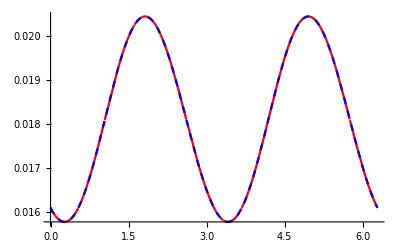

```mathematica
Plot[{J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}],J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]},{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 12; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ)+EulerGamma+-∞+∞ encountered.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression -(ⅈ (0.+0. ⅈ) ComplexInfinity)/(4 π) encountered.

CompiledFunction::cfse: Compiled expression Indeterminate should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 12; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ)+EulerGamma+-∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression Indeterminate should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

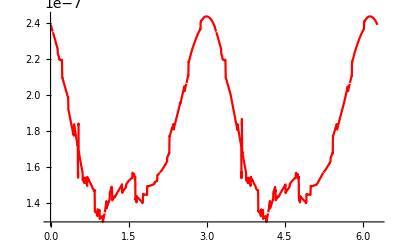

```mathematica
Plot[J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1,{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

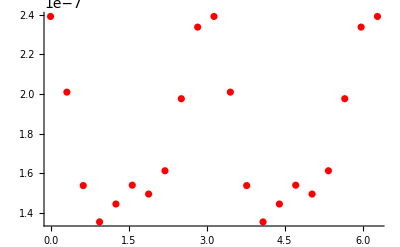

```mathematica
ListPlot[Table[{ϕ,J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1},{ϕ,0,2π,0.1π}],PlotStyle->{{Red},{Blue,Dashed}}]
```

## Dipole Cross Section

```mathematica
dσ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
dσHZ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
J2HZ[{kT Cos[ϕ],kT Sin[ϕ]},{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]
]
```

```mathematica
showdσ[bu_,x1u_,x3u_,kT_]:=Module[{ϕ,x2u,x4u,v2},
x2u=-x1u;x4u=-x3u;
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[Plot[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]];
Print[ParametricPlot[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
v2=NIntegrate[dσ[bu+x1u,bu+x2u,x3u,x4u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}];
Print["v_2=",v2];
v2
]
```

```mathematica
showdσHZ[bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[bu+x1u,bu+x2u,x3u,x4u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]
]
```

## b = 1

### kT = 1.0

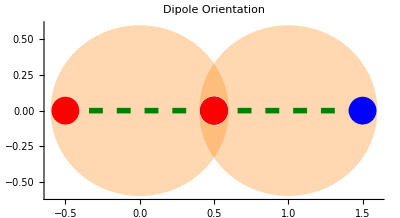

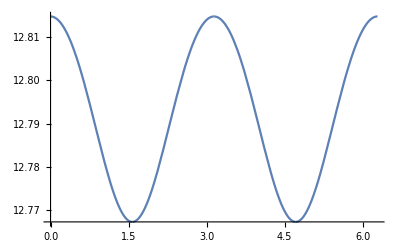

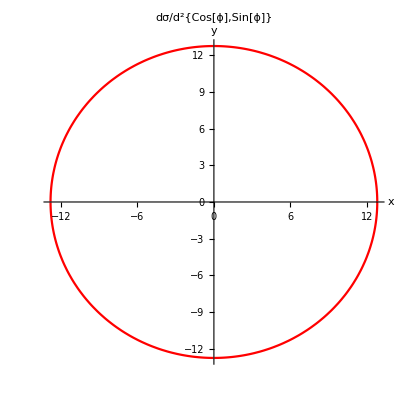

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$12444724 near {ϕ$12444724} = {0.198042}. NIntegrate obtained 0.0743763+0. ⅈ and 2.35141×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$12444724 near {ϕ$12444724} = {0.785301}. NIntegrate obtained 4.12919×10^-7+0. ⅈ and 1.01458×10^-7 for the integral and error estimates.

v_2={0.000925367,5.13742×10^-9}

```mathematica
x1u=1/2{1,0};
x3u=1/2{1,0};
bu={1,10^-10};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
```

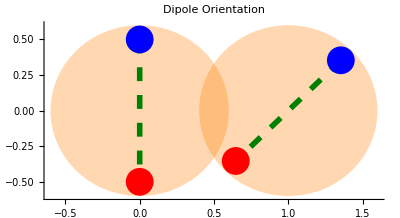

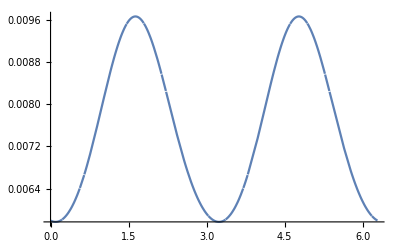

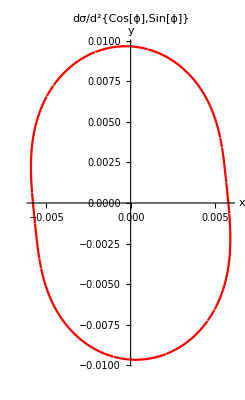

v_2={-0.127005+0. ⅈ,-0.0184846+0. ⅈ}

```mathematica
x1u=1/2{Cos[π/4],Sin[π/4]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
```

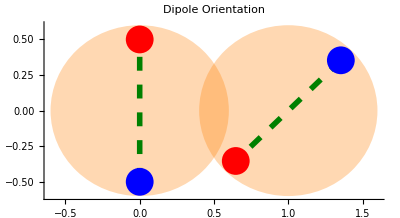

-Graphics-

-Graphics-

v_2={-0.127005+0. ⅈ,-0.0184846+0. ⅈ}

```mathematica
x1u=1/2{Cos[π/4],Sin[π/4]};
x3u=1/2{Cos[-π/2],Sin[-π/2]};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
```

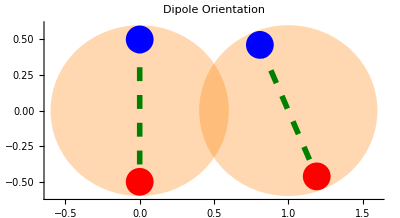

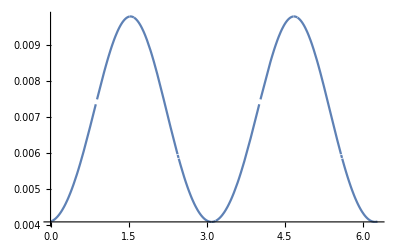

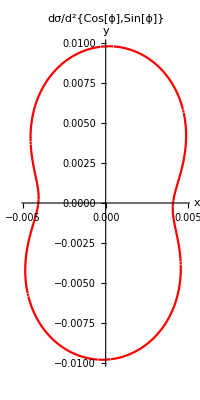

v_2={-0.2097+0. ⅈ,0.0161542}

```mathematica
x1u=1/2{Cos[5π/8],Sin[5π/8]};
x3u=1/2{0,1};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
```

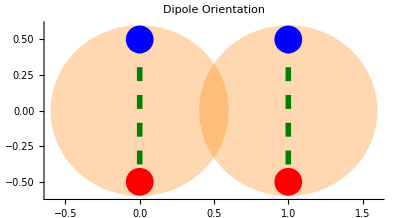

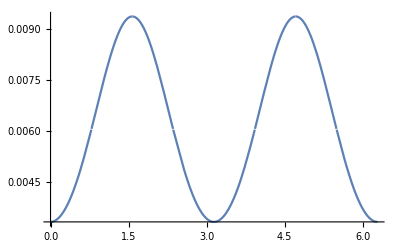

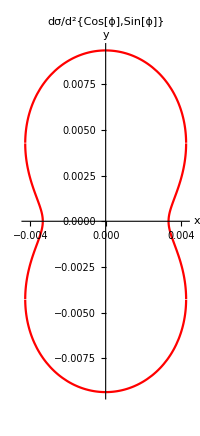

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$11646218 near {ϕ$11646218} = {0.0000241858}. NIntegrate obtained 1.32679×10^-17+0. ⅈ and 7.44428×10^-18 for the integral and error estimates.

v_2={-0.242273+0. ⅈ,3.40479×10^-16}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
```

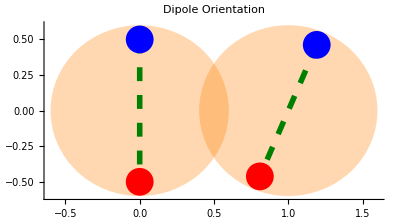

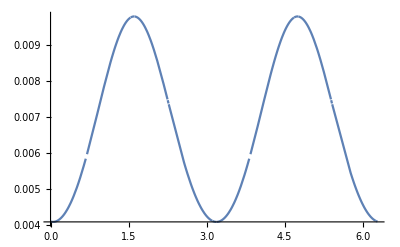

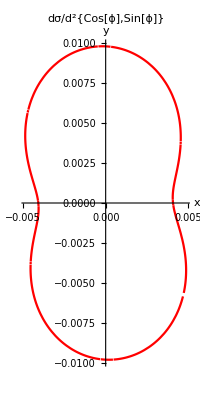

v_2={-0.2097+0. ⅈ,-0.0161542+0. ⅈ}

```mathematica
x1u=1/2{Cos[3π/8],Sin[3π/8]};
x3u=1/2{0,1};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
```

```mathematica
x1u=1/2{Cos[2π/8],Sin[2π/8]};
x3u=1/2{0,1};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
```

-Graphics-

-Graphics-

-Graphics-

v_2={-0.127005+0. ⅈ,-0.0184846+0. ⅈ}

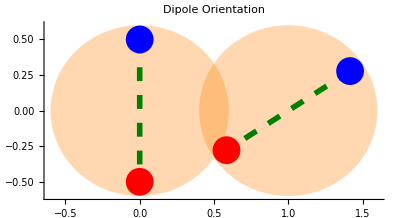

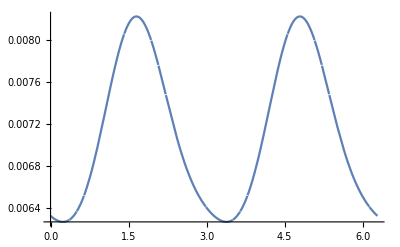

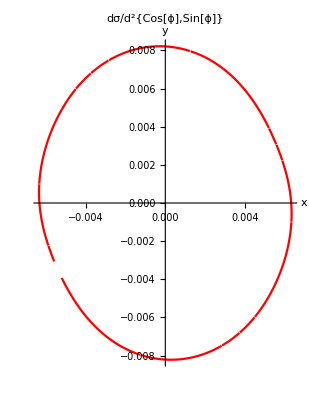

v_2={-0.0659241+0. ⅈ,-0.0161236+0. ⅈ}

```mathematica
x1u=1/2{Cos[3π/16],Sin[3π/16]};
x3u=1/2{0,1};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
```

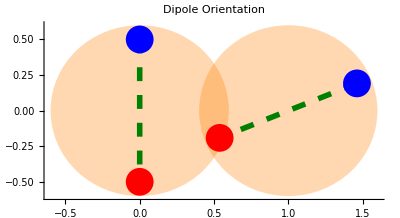

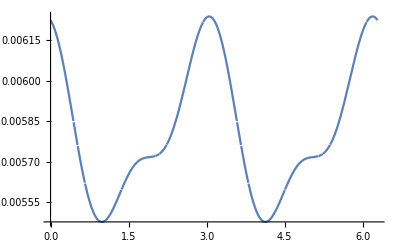

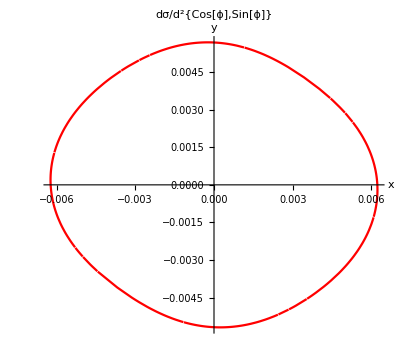

v_2={0.0236373,-0.012436+0. ⅈ}

```mathematica
x1u=1/2{Cos[1π/8],Sin[1π/8]};
x3u=1/2{0,1};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
```

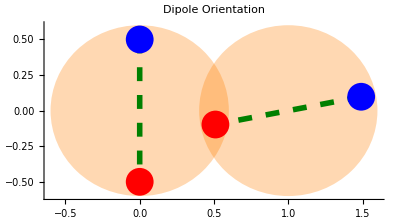

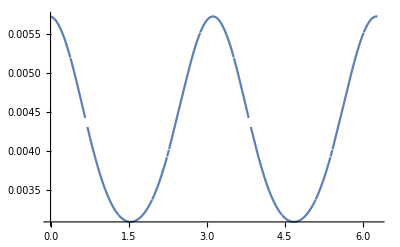

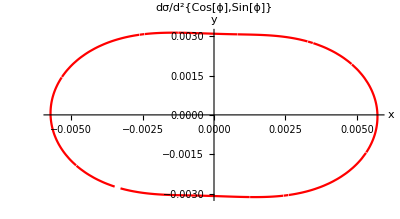

v_2={0.153374,-0.00719185+0. ⅈ}

```mathematica
x1u=1/2{Cos[π/16],Sin[π/16]};
x3u=1/2{0,1};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
```

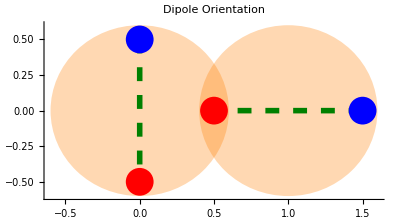

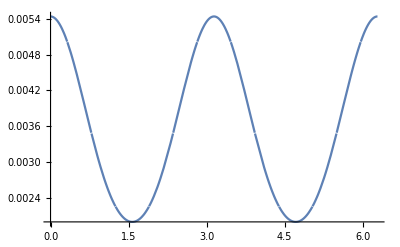

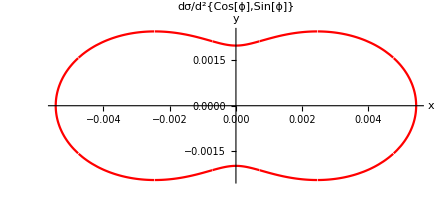

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$16343374 near {ϕ$16343374} = {0.0000241858}. NIntegrate obtained 1.70288×10^-17+7.07499×10^-20 ⅈ and 1.35438×10^-17 for the integral and error estimates.

v_2={0.239614,7.53091×10^-16+3.12889×10^-18 ⅈ}

```mathematica
x1u=1/2{Cos[0],Sin[0]};
x3u=1/2{0,1};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
```

```mathematica
Point
```

```mathematica
Graphics[Point[Re[{{0.023637288757153874,-0.012436042788294336+0. ⅈ},{0.15337373915305566,-0.007191848467836517+0. ⅈ},{0.23961398870630143,7.530913148631375*^-16+3.1288919261538432*^-18 ⅈ}}]]]
```

-Graphics-

```mathematica
v2dipole=Re[{{-0.24227288570153577+0. ⅈ,3.4047948464247705*^-16},{-0.2097001936783897+0. ⅈ,-0.016154248924980553+0. ⅈ},{-0.1270045794577177+0. ⅈ,-0.018484558033608933+0. ⅈ},{-0.06592410440076976+0. ⅈ,-0.0161235692088982+0. ⅈ},{0.023637288757153874,-0.012436042788294336+0. ⅈ},{0.15337373915305566,-0.007191848467836517+0. ⅈ},{0.23961398870630143,7.530913148631375*^-16+3.1288919261538432*^-18 ⅈ}}];
```

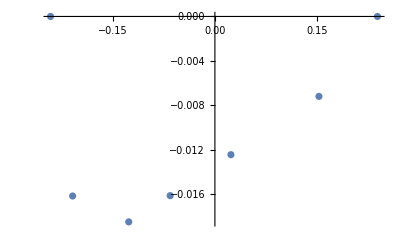

```mathematica
ListPlot[v2dipole,Joined->False]
```

```mathematica
Length[v2dipole]
```

7

```mathematica
phi2={π/2,(3π)/8,2π/8,3π/16,π/8,π/16,0}
```

{π/2,(3 π)/8,π/4,(3 π)/16,π/8,π/16,0}

```mathematica
Length[phi2]
```

7

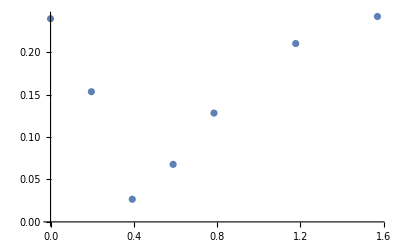

```mathematica
ListPlot[Transpose[{phi2,Sqrt[v2dipole[[All,1]]^2+v2dipole[[All,2]]^2]}],Joined->False]
```

#### any kT

### r = 1

```mathematica
v2kT={};
```

-Graphics-

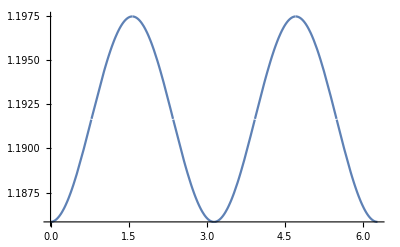

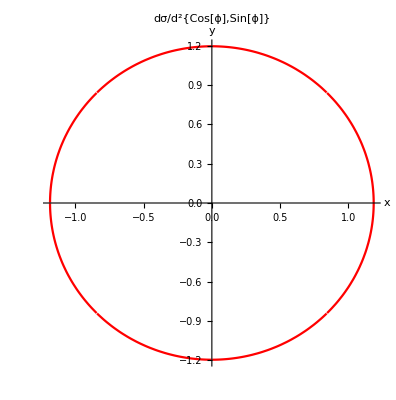

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$22233616 near {ϕ$22233616} = {0.0000241858}. NIntegrate obtained 2.57433×10^-15+0. ⅈ and 2.49445×10^-15 for the integral and error estimates.

v_2={-0.00243754+0. ⅈ,3.43825×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.1;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

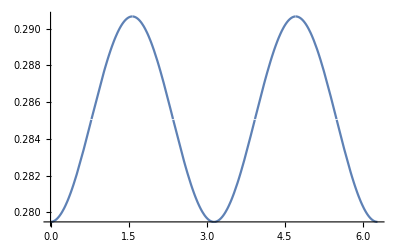

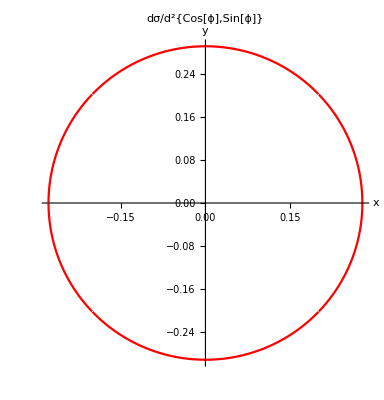

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$22569477 near {ϕ$22569477} = {0.503048}. NIntegrate obtained 5.10009×10^-16+0. ⅈ and 1.97399×10^-16 for the integral and error estimates.

v_2={-0.0098084+0. ⅈ,2.8475×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.2;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

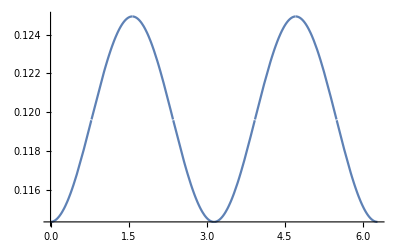

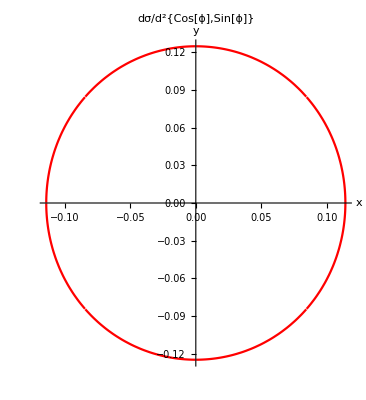

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$22900019 near {ϕ$22900019} = {0.0000241858}. NIntegrate obtained 2.24213×10^-16+0. ⅈ and 2.17873×10^-16 for the integral and error estimates.

v_2={-0.0221919+0. ⅈ,2.9832×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.3;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

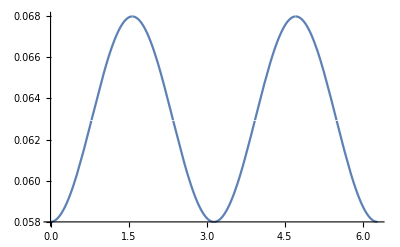

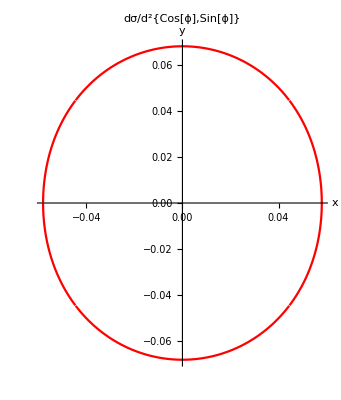

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$23239045 near {ϕ$23239045} = {0.0000241858}. NIntegrate obtained 6.40492×10^-17+0. ⅈ and 1.20953×10^-16 for the integral and error estimates.

v_2={-0.0396154+0. ⅈ,1.61912×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.4;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

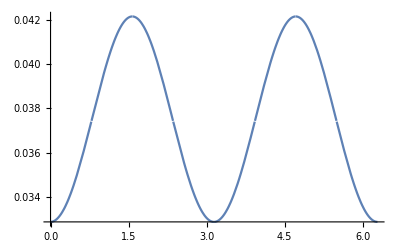

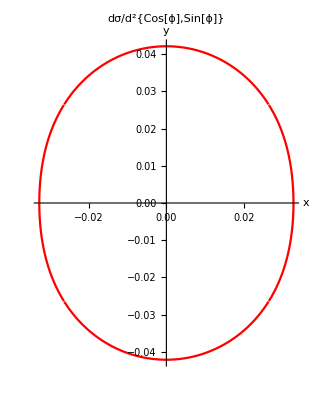

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$23565053 near {ϕ$23565053} = {0.0000241858}. NIntegrate obtained 1.99764×10^-17+0. ⅈ and 7.92985×10^-17 for the integral and error estimates.

v_2={-0.0620339+0. ⅈ,8.48684×10^-17}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

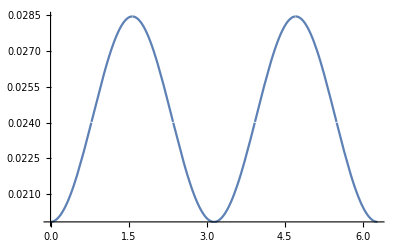

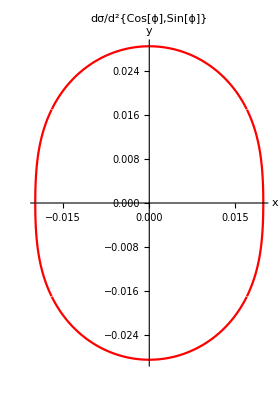

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$23891856 near {ϕ$23891856} = {0.0000241858}. NIntegrate obtained -2.81622×10^-17+0. ⅈ and 4.02372×10^-17 for the integral and error estimates.

v_2={-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.6;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

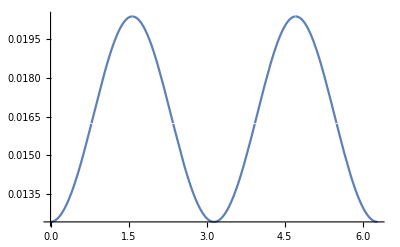

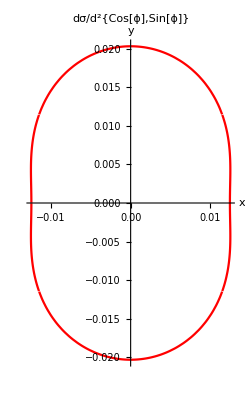

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$24258178 near {ϕ$24258178} = {2.60153}. NIntegrate obtained 3.36103×10^-17+0. ⅈ and 8.83935×10^-18 for the integral and error estimates.

v_2={-0.121298+0. ⅈ,3.27922×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.7;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

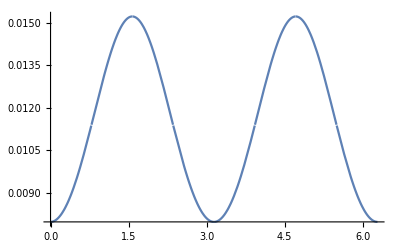

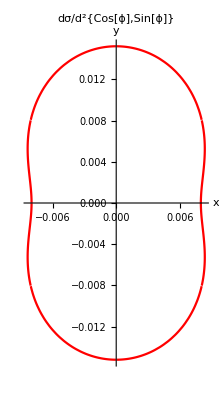

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$24647273 near {ϕ$24647273} = {0.0000241858}. NIntegrate obtained 5.85469×10^-18+0. ⅈ and 1.58722×10^-17 for the integral and error estimates.

v_2={-0.157685+0. ⅈ,8.10914×10^-17}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.8;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

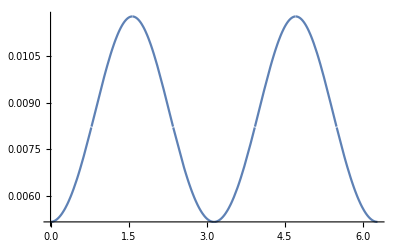

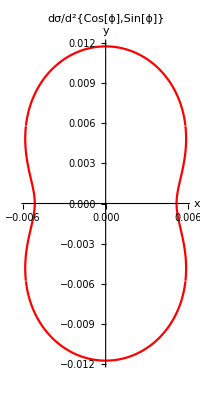

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$25035047 near {ϕ$25035047} = {0.0000241858}. NIntegrate obtained -7.87402×10^-18+0. ⅈ and 1.11461×10^-17 for the integral and error estimates.

v_2={-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.9;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$25405840 near {ϕ$25405840} = {0.0000241858}. NIntegrate obtained 1.32679×10^-17+0. ⅈ and 7.44428×10^-18 for the integral and error estimates.

v_2={-0.242273+0. ⅈ,3.40479×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}}}

-Graphics-

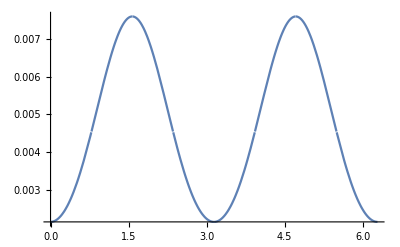

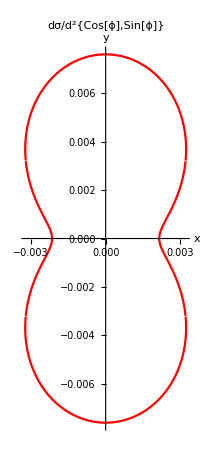

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$25803385 near {ϕ$25803385} = {2.25792}. NIntegrate obtained 2.10742×10^-18+0. ⅈ and 2.52612×10^-18 for the integral and error estimates.

v_2={-0.289532+0. ⅈ,7.12635×10^-17}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.1;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

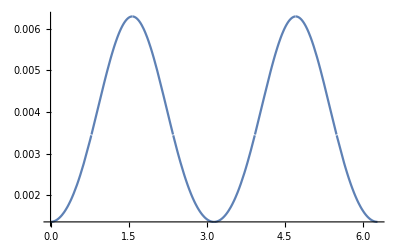

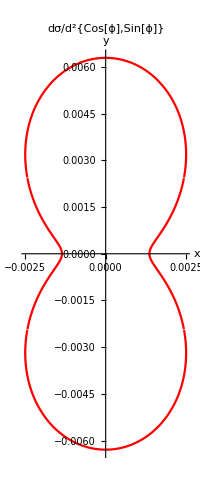
-Graphics-kT=1.0
x1u=1/2{1,0};
x3u=1/2{1,0};
bu={1,10^-10};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$12444724 near {ϕ$12444724} = {0.198042}. NIntegrate obtained 0.0743763+0. ⅈ and 2.35141×10^-7 for the integral and error estimates.
NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$12444724 near {ϕ$12444724} = {0.785301}. NIntegrate obtained 4.12919×10^-7+0. ⅈ and 1.01458×10^-7 for the integral and error estimates.
v_2={0.000925367,5.13742×10^-9}
x1u=1/2{Cos[π/4],Sin[π/4]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
-Graphics-

-Graphics-
-Graphics-
v_2={-0.127005+0. ⅈ,-0.0184846+0. ⅈ}
x1u=1/2{Cos[π/4],Sin[π/4]};
x3u=1/2{Cos[-π/2],Sin[-π/2]};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
-Graphics-

-Graphics-
-Graphics-
v_2={-0.127005+0. ⅈ,-0.0184846+0. ⅈ}
x1u=1/2{Cos[5π/8],Sin[5π/8]};
x3u=1/2{0,1};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
-Graphics-

-Graphics-
-Graphics-
v_2={-0.2097+0. ⅈ,0.0161542}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$11646218 near {ϕ$11646218} = {0.0000241858}. NIntegrate obtained 1.32679×10^-17+0. ⅈ and 7.44428×10^-18 for the integral and error estimates.
v_2={-0.242273+0. ⅈ,3.40479×10^-16}
x1u=1/2{Cos[3π/8],Sin[3π/8]};
x3u=1/2{0,1};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
-Graphics-

-Graphics-
-Graphics-
v_2={-0.2097+0. ⅈ,-0.0161542+0. ⅈ}
x1u=1/2{Cos[2π/8],Sin[2π/8]};
x3u=1/2{0,1};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
-Graphics-

-Graphics-
-Graphics-
v_2={-0.127005+0. ⅈ,-0.0184846+0. ⅈ}
x1u=1/2{Cos[3π/16],Sin[3π/16]};
x3u=1/2{0,1};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
-Graphics-

-Graphics-
-Graphics-
v_2={-0.0659241+0. ⅈ,-0.0161236+0. ⅈ}
x1u=1/2{Cos[1π/8],Sin[1π/8]};
x3u=1/2{0,1};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
-Graphics-

-Graphics-
-Graphics-
v_2={0.0236373,-0.012436+0. ⅈ}
x1u=1/2{Cos[π/16],Sin[π/16]};
x3u=1/2{0,1};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
-Graphics-

-Graphics-
-Graphics-
v_2={0.153374,-0.00719185+0. ⅈ}
x1u=1/2{Cos[0],Sin[0]};
x3u=1/2{0,1};
bu={1,0};
kT=1.0;
showdσ[bu,x1u,x3u,kT]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$16343374 near {ϕ$16343374} = {0.0000241858}. NIntegrate obtained 1.70288×10^-17+7.07499×10^-20 ⅈ and 1.35438×10^-17 for the integral and error estimates.
v_2={0.239614,7.53091×10^-16+3.12889×10^-18 ⅈ}
Point
Graphics[Point[Re[{{0.0236373,-0.012436+0. ⅈ},{0.153374,-0.00719185+0. ⅈ},{0.239614,7.53091×10^-16+3.12889×10^-18 ⅈ}}]]]
-Graphics-
v2dipole=Re[{{-0.242273+0. ⅈ,3.40479×10^-16},{-0.2097+0. ⅈ,-0.0161542+0. ⅈ},{-0.127005+0. ⅈ,-0.0184846+0. ⅈ},{-0.0659241+0. ⅈ,-0.0161236+0. ⅈ},{0.0236373,-0.012436+0. ⅈ},{0.153374,-0.00719185+0. ⅈ},{0.239614,7.53091×10^-16+3.12889×10^-18 ⅈ}}];
ListPlot[v2dipole,Joined→False]
-Graphics-
Length[v2dipole]
7
phi2={π/2,(3π)/8,2π/8,3π/16,π/8,π/16,0}
{π/2,(3 π)/8,π/4,(3 π)/16,π/8,π/16,0}
Length[phi2]
7
ListPlot[Transpose[{phi2,Sqrt[v2dipole[[All,1]]^2+v2dipole[[All,2]]^2]}],Joined→False]
-Graphics-
any kT
v2kT={};
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.1;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$22233616 near {ϕ$22233616} = {0.0000241858}. NIntegrate obtained 2.57433×10^-15+0. ⅈ and 2.49445×10^-15 for the integral and error estimates.
v_2={-0.00243754+0. ⅈ,3.43825×10^-16}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.2;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$22569477 near {ϕ$22569477} = {0.503048}. NIntegrate obtained 5.10009×10^-16+0. ⅈ and 1.97399×10^-16 for the integral and error estimates.
v_2={-0.0098084+0. ⅈ,2.8475×10^-16}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.3;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$22900019 near {ϕ$22900019} = {0.0000241858}. NIntegrate obtained 2.24213×10^-16+0. ⅈ and 2.17873×10^-16 for the integral and error estimates.
v_2={-0.0221919+0. ⅈ,2.9832×10^-16}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.4;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$23239045 near {ϕ$23239045} = {0.0000241858}. NIntegrate obtained 6.40492×10^-17+0. ⅈ and 1.20953×10^-16 for the integral and error estimates.
v_2={-0.0396154+0. ⅈ,1.61912×10^-16}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$23565053 near {ϕ$23565053} = {0.0000241858}. NIntegrate obtained 1.99764×10^-17+0. ⅈ and 7.92985×10^-17 for the integral and error estimates.
v_2={-0.0620339+0. ⅈ,8.48684×10^-17}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.6;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$23891856 near {ϕ$23891856} = {0.0000241858}. NIntegrate obtained -2.81622×10^-17+0. ⅈ and 4.02372×10^-17 for the integral and error estimates.
v_2={-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.7;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$24258178 near {ϕ$24258178} = {2.60153}. NIntegrate obtained 3.36103×10^-17+0. ⅈ and 8.83935×10^-18 for the integral and error estimates.
v_2={-0.121298+0. ⅈ,3.27922×10^-16}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.8;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$24647273 near {ϕ$24647273} = {0.0000241858}. NIntegrate obtained 5.85469×10^-18+0. ⅈ and 1.58722×10^-17 for the integral and error estimates.
v_2={-0.157685+0. ⅈ,8.10914×10^-17}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.9;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$25035047 near {ϕ$25035047} = {0.0000241858}. NIntegrate obtained -7.87402×10^-18+0. ⅈ and 1.11461×10^-17 for the integral and error estimates.
v_2={-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$25405840 near {ϕ$25405840} = {0.0000241858}. NIntegrate obtained 1.32679×10^-17+0. ⅈ and 7.44428×10^-18 for the integral and error estimates.
v_2={-0.242273+0. ⅈ,3.40479×10^-16}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.1;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$25803385 near {ϕ$25803385} = {2.25792}. NIntegrate obtained 2.10742×10^-18+0. ⅈ and 2.52612×10^-18 for the integral and error estimates.
v_2={-0.289532+0. ⅈ,7.12635×10^-17}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.2;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$26188966 near {ϕ$26188966} = {1.14118}. NIntegrate obtained -3.07642×10^-18+0. ⅈ and 1.99011×10^-18 for the integral and error estimates.
v_2={-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.3;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$26566626 near {ϕ$26566626} = {0.822116}. NIntegrate obtained -2.18196×10^-18+0. ⅈ and 1.50195×10^-18 for the integral and error estimates.
v_2={-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.4;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$26944030 near {ϕ$26944030} = {2.28247}. NIntegrate obtained -2.71051×10^-18+0. ⅈ and 1.47598×10^-18 for the integral and error estimates.
v_2={-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$27342164 near {ϕ$27342164} = {0.920291}. NIntegrate obtained 9.21572×10^-19+0. ⅈ and 1.07721×10^-18 for the integral and error estimates.
v_2={-0.493546+0. ⅈ,7.943×10^-17}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$27727248 near {ϕ$27727248} = {0.858932}. NIntegrate obtained 2.29377×10^-18+0. ⅈ and 8.5747×10^-19 for the integral and error estimates.
v_2={-0.606603+0. ⅈ,3.11017×10^-16}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=2.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$28119092 near {ϕ$28119092} = {1.178}. NIntegrate obtained -1.53912×10^-18+0. ⅈ and 5.68968×10^-19 for the integral and error estimates.
v_2={-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=2.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$28582005 near {ϕ$28582005} = {2.23338}. NIntegrate obtained -1.34509×10^-18+0. ⅈ and 5.32879×10^-19 for the integral and error estimates.
v_2={-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=2.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$29074717 near {ϕ$29074717} = {2.25792}. NIntegrate obtained 7.7927×10^-20+0. ⅈ and 4.92233×10^-19 for the integral and error estimates.
v_2={-0.664932+0. ⅈ,2.14288×10^-17}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=2.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$29568935 near {ϕ$29568935} = {2.06157}. NIntegrate obtained -1.01983×10^-18+0. ⅈ and 5.71921×10^-19 for the integral and error estimates.
v_2={-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=3.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$30090867 near {ϕ$30090867} = {2.01249}. NIntegrate obtained -4.06576×10^-19+0. ⅈ and 5.09201×10^-19 for the integral and error estimates.
v_2={-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=3.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$30617974 near {ϕ$30617974} = {0.0000241858}. NIntegrate obtained -6.33157×10^-19+0. ⅈ and 1.03203×10^-18 for the integral and error estimates.
v_2={-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=3.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$31127020 near {ϕ$31127020} = {0.0000241858}. NIntegrate obtained 7.07061×10^-19+0. ⅈ and 1.21397×10^-18 for the integral and error estimates.
v_2={-0.501266+0. ⅈ,2.3872×10^-16}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=3.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$31620722 near {ϕ$31620722} = {0.0000241858}. NIntegrate obtained -2.95106×10^-18+0. ⅈ and 1.33214×10^-18 for the integral and error estimates.
v_2={-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=4.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$32120680 near {ϕ$32120680} = {0.674854}. NIntegrate obtained 5.04832×10^-19+0. ⅈ and 1.31251×10^-18 for the integral and error estimates.
v_2={-0.467766+0. ⅈ,1.96087×10^-16}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=4.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$32618210 near {ϕ$32618210} = {0.822116}. NIntegrate obtained 6.50521×10^-19+0. ⅈ and 1.71884×10^-18 for the integral and error estimates.
v_2={-0.460269+0. ⅈ,2.79431×10^-16}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=4.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$33122676 near {ϕ$33122676} = {2.41746}. NIntegrate obtained 1.999×10^-19+0. ⅈ and 1.63337×10^-18 for the integral and error estimates.
v_2={-0.457377+0. ⅈ,9.70988×10^-17}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=4.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$33627852 near {ϕ$33627852} = {0.84666}. NIntegrate obtained 1.63308×10^-18+0. ⅈ and 2.74586×10^-18 for the integral and error estimates.
v_2={-0.458429+0. ⅈ,9.17943×10^-16}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=5.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$34164679 near {ϕ$34164679} = {2.22111}. NIntegrate obtained 3.92515×10^-18+0. ⅈ and 3.18254×10^-18 for the integral and error estimates.
v_2={-0.463108+0. ⅈ,2.61457×10^-15}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}}}
showdσHZ[bu,x1u,x3u,kT]
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$34717038 near {ϕ$34717038} = {1.01847}. NIntegrate obtained -2.05861×10^-12 and 1.2748×10^-12 for the integral and error estimates.
{-0.463108,-1.37125×10^-9}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=5.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$34827593 near {ϕ$34827593} = {2.33155}. NIntegrate obtained -3.60497×10^-18+0. ⅈ and 3.26968×10^-18 for the integral and error estimates.
v_2={-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=5.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$35363065 near {ϕ$35363065} = {2.50336}. NIntegrate obtained 2.77954×10^-18+0. ⅈ and 4.31198×10^-18 for the integral and error estimates.
v_2={-0.483405+0. ⅈ,2.80211×10^-15}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=5.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$35901002 near {ϕ$35901002} = {0.748485}. NIntegrate obtained -2.88838×10^-19+0. ⅈ and 3.10996×10^-18 for the integral and error estimates.
v_2={-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=6.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$36441489 near {ϕ$36441489} = {2.47882}. NIntegrate obtained 5.19104×10^-18+0. ⅈ and 4.81235×10^-18 for the integral and error estimates.
v_2={-0.520401+0. ⅈ,8.82195×10^-15}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=6.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$36989626 near {ϕ$36989626} = {0.65031}. NIntegrate obtained -2.9661×10^-18+0. ⅈ and 3.98539×10^-18 for the integral and error estimates.
v_2={-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=6.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$37544909 near {ϕ$37544909} = {2.50336}. NIntegrate obtained -3.51085×10^-18+0. ⅈ and 5.16886×10^-18 for the integral and error estimates.
v_2={-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=6.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$38107113 near {ϕ$38107113} = {2.28247}. NIntegrate obtained -1.16183×10^-17+0. ⅈ and 4.21943×10^-18 for the integral and error estimates.
v_2={-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=7.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$38658935 near {ϕ$38658935} = {0.969378}. NIntegrate obtained -1.7087×10^-17+0. ⅈ and 4.05027×10^-18 for the integral and error estimates.
v_2={-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=7.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$39193941 near {ϕ$39193941} = {2.22111}. NIntegrate obtained -1.72414×10^-18+0. ⅈ and 5.36369×10^-18 for the integral and error estimates.
v_2={-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=7.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$39777025 near {ϕ$39777025} = {2.18429}. NIntegrate obtained 6.65526×10^-18+0. ⅈ and 5.09018×10^-18 for the integral and error estimates.
v_2={-0.626094+0. ⅈ,1.02341×10^-13}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=7.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$40449219 near {ϕ$40449219} = {0.944835}. NIntegrate obtained 9.31906×10^-18+0. ⅈ and 7.58834×10^-18 for the integral and error estimates.
v_2={-0.509444+0. ⅈ,1.97668×10^-13}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=8.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$41134787 near {ϕ$41134787} = {2.17202}. NIntegrate obtained 1.88269×10^-18+0. ⅈ and 1.04716×10^-17 for the integral and error estimates.
v_2={-0.312699+0. ⅈ,4.85387×10^-14}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}}}
showdσHZ[bu,x1u,x3u,kT]
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$41827073 near {ϕ$41827073} = {2.95742}. NIntegrate obtained -5.81201×10^-15 and 8.90176×10^-13 for the integral and error estimates.
{-0.3127,-1.49843×10^-10}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=8.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$41978991 near {ϕ$41978991} = {2.29474}. NIntegrate obtained -2.29538×10^-17+0. ⅈ and 2.02749×10^-17 for the integral and error estimates.
v_2={-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=8.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$42666724 near {ϕ$42666724} = {0.84666}. NIntegrate obtained -4.67437×10^-17+0. ⅈ and 2.33295×10^-17 for the integral and error estimates.
v_2={0.0293956,-1.22152×10^-12+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=8.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$43343733 near {ϕ$43343733} = {2.33155}. NIntegrate obtained -1.30332×10^-17+0. ⅈ and 3.26071×10^-17 for the integral and error estimates.
v_2={0.0991137,-3.14959×10^-13+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=9.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$44022180 near {ϕ$44022180} = {2.34382}. NIntegrate obtained -2.14631×10^-16+0. ⅈ and 4.04524×10^-17 for the integral and error estimates.
v_2={0.12317,-4.81401×10^-12+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=9.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$44702342 near {ϕ$44702342} = {0.883475}. NIntegrate obtained -7.23042×10^-17+0. ⅈ and 5.02032×10^-17 for the integral and error estimates.
v_2={0.123017,-1.54057×10^-12+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=9.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$45387184 near {ϕ$45387184} = {0.797572}. NIntegrate obtained 7.60238×10^-17+0. ⅈ and 8.73176×10^-17 for the integral and error estimates.
v_2={0.110969,1.58621×10^-12}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=9.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$46070838 near {ϕ$46070838} = {2.28247}. NIntegrate obtained 8.23575×10^-17+0. ⅈ and 8.42158×10^-17 for the integral and error estimates.
v_2={0.0929297,1.73677×10^-12}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=10.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$46754320 near {ϕ$46754320} = {2.23338}. NIntegrate obtained -1.68858×10^-16+0. ⅈ and 7.2551×10^-17 for the integral and error estimates.
v_2={0.071308,-3.70985×10^-12+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=10.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$47442360 near {ϕ$47442360} = {0.834388}. NIntegrate obtained -4.8105×10^-16+0. ⅈ and 9.63035×10^-17 for the integral and error estimates.
v_2={0.046731,-1.13229×10^-11+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=10.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$48153117 near {ϕ$48153117} = {0.883475}. NIntegrate obtained -4.766×10^-17+0. ⅈ and 1.054×10^-16 for the integral and error estimates.
v_2={0.0189289,-1.23227×10^-12+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=10.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$48847741 near {ϕ$48847741} = {2.22111}. NIntegrate obtained 2.76484×10^-16+0. ⅈ and 1.54643×10^-16 for the integral and error estimates.
v_2={-0.0127807+0. ⅈ,8.02354×10^-12}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=11.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$49551406 near {ϕ$49551406} = {2.27019}. NIntegrate obtained 8.69857×10^-16+0. ⅈ and 1.92874×10^-16 for the integral and error estimates.
v_2={-0.0491407+0. ⅈ,2.88322×10^-11}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}}}
showdσHZ[bu,x1u,x3u,kT]
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$50255325 near {ϕ$50255325} = {3.706}. NIntegrate obtained -1.48263×10^-6 and 3.52391×10^-12 for the integral and error estimates.
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$50255325 near {ϕ$50255325} = {3.706}. NIntegrate obtained -2.65441×10^-14 and 1.937×10^-12 for the integral and error estimates.
{-0.0491431,-8.79825×10^-10}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=11.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$50361508 near {ϕ$50361508} = {0.957106}. NIntegrate obtained 2.15498×10^-16+0. ⅈ and 1.93393×10^-16 for the integral and error estimates.
v_2={-0.0905752+0. ⅈ,8.26214×10^-12}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=11.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$51067207 near {ϕ$51067207} = {2.24565}. NIntegrate obtained -4.3545×10^-17+0. ⅈ and 2.32221×10^-16 for the integral and error estimates.
v_2={-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=11.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$51760150 near {ϕ$51760150} = {0.662582}. NIntegrate obtained 4.02214×10^-16+0. ⅈ and 4.00041×10^-16 for the integral and error estimates.
v_2={-0.185819+0. ⅈ,2.09273×10^-11}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=12.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$52459132 near {ϕ$52459132} = {0.760757}. NIntegrate obtained -3.77966×10^-16+0. ⅈ and 5.30339×10^-16 for the integral and error estimates.
v_2={-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=12.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$53150249 near {ϕ$53150249} = {0.748485}. NIntegrate obtained 5.79877×10^-16+0. ⅈ and 6.93605×10^-16 for the integral and error estimates.
v_2={-0.277796+0. ⅈ,3.9952×10^-11}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=12.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$53843153 near {ϕ$53843153} = {2.42973}. NIntegrate obtained -1.80718×10^-15+0. ⅈ and 9.42879×10^-16 for the integral and error estimates.
v_2={-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=12.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$54531737 near {ϕ$54531737} = {2.38064}. NIntegrate obtained -1.80047×10^-15+0. ⅈ and 1.92618×10^-15 for the integral and error estimates.
v_2={-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=13.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$55221973 near {ϕ$55221973} = {2.29474}. NIntegrate obtained 2.86021×10^-15+0. ⅈ and 1.53065×10^-15 for the integral and error estimates.
v_2={-0.328691+0. ⅈ,2.66774×10^-10}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}}}
showdσHZ[bu,x1u,x3u,kT]
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$55926032 near {ϕ$55926032} = {5.03136}. NIntegrate obtained 8.34509×10^-15 and 4.27678×10^-13 for the integral and error estimates.
{-0.328691,7.78354×10^-10}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=13.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$56070345 near {ϕ$56070345} = {2.39291}. NIntegrate obtained -1.29258×10^-14+0. ⅈ and 3.2129×10^-15 for the integral and error estimates.
v_2={-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=13.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$56786507 near {ϕ$56786507} = {2.49109}. NIntegrate obtained 6.77554×10^-16+0. ⅈ and 3.01841×10^-15 for the integral and error estimates.
v_2={-0.284242+0. ⅈ,7.26712×10^-11}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=13.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$57502891 near {ϕ$57502891} = {0.736213}. NIntegrate obtained 4.67769×10^-15+0. ⅈ and 4.33086×10^-15 for the integral and error estimates.
v_2={-0.244547+0. ⅈ,5.35399×10^-10}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=14.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$58215605 near {ϕ$58215605} = {0.748485}. NIntegrate obtained 3.70163×10^-15+0. ⅈ and 8.24761×10^-15 for the integral and error estimates.
v_2={-0.197058+0. ⅈ,4.53068×10^-10}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=14.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$58923137 near {ϕ$58923137} = {0.723941}. NIntegrate obtained 7.87763×10^-15+0. ⅈ and 8.85538×10^-15 for the integral and error estimates.
v_2={-0.144133+0. ⅈ,1.03534×10^-9}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=14.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$59642346 near {ϕ$59642346} = {0.736213}. NIntegrate obtained -9.62478×10^-15+0. ⅈ and 1.01384×10^-14 for the integral and error estimates.
v_2={-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=14.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$60389568 near {ϕ$60389568} = {2.34382}. NIntegrate obtained 3.11909×10^-14+0. ⅈ and 1.37116×10^-14 for the integral and error estimates.
v_2={-0.0302958+0. ⅈ,4.78307×10^-9}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=15.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$61184647 near {ϕ$61184647} = {0.760757}. NIntegrate obtained 1.73559×10^-14+0. ⅈ and 1.43709×10^-14 for the integral and error estimates.
v_2={0.0257867,2.87951×10^-9}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=15.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$62780740 near {ϕ$62780740} = {2.39291}. NIntegrate obtained -1.55478×10^-14+0. ⅈ and 1.68176×10^-14 for the integral and error estimates.
v_2={0.0769879,-2.78018×10^-9+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=15.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$63566758 near {ϕ$63566758} = {0.748485}. NIntegrate obtained 3.85334×10^-14+0. ⅈ and 1.83687×10^-14 for the integral and error estimates.
v_2={0.119314,7.36681×10^-9}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=15.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$64334113 near {ϕ$64334113} = {2.28247}. NIntegrate obtained -5.80067×10^-14+0. ⅈ and 2.10961×10^-14 for the integral and error estimates.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-7.875 Sin[ϕ$64334113])) (-(1+ⅇ^(ⅈ (0.-15.75 Cos[«1»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-7.875 Sin[ϕ$64334113])) (-(1+ⅇ^(ⅈ (0.-15.75 Cos[«1»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+7.875 Sin[ϕ$64334113])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+7.875 Sin[ϕ$64334113])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.
NIntegrate::levmaxord: (15.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+15.75 Cos[ϕ$64334113])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+15.75 Cos[ϕ$64334113])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-15.75 Cos[ϕ$64334113])]))/Abs[0.-15.75 Sin[ϕ$64334113]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (15.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+15.75 Cos[ϕ$64334113])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+15.75 Cos[ϕ$64334113])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-15.75 Cos[ϕ$64334113])]))/Abs[0.-15.75 Sin[ϕ$64334113]] as a non-Levin function.
General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.
v_2={0.148945,-1.17199×10^-8+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=16.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$65104689 near {ϕ$65104689} = {2.27019}. NIntegrate obtained -7.39578×10^-14+0. ⅈ and 2.2683×10^-14 for the integral and error estimates.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8. Sin[ϕ$65104689])) (-(1+ⅇ^(ⅈ (0.-16. Cos[«1»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[ϕ$65104689]-(0.+16. ⅈ) Sin[ϕ$65104689])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16. Cos[«1»]-16. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16. Cos[«1»]-16. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[«1»]-(0.+16. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8. Sin[ϕ$65104689])) (-(1+ⅇ^(ⅈ (0.-16. Cos[«1»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[ϕ$65104689]-(0.+16. ⅈ) Sin[ϕ$65104689])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16. Cos[«1»]-16. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16. Cos[«1»]-16. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[«1»]-(0.+16. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) as a non-Levin function.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8. Sin[ϕ$65104689])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[ϕ$65104689]+(0.+16. ⅈ) Sin[ϕ$65104689])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16. Cos[«1»]+16. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16. Cos[«1»]+16. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[«1»]+(0.+16. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 Plus[«3»]]+CosIntegral[1/2 ⅈ Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8. Sin[ϕ$65104689])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[ϕ$65104689]+(0.+16. ⅈ) Sin[ϕ$65104689])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16. Cos[«1»]+16. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16. Cos[«1»]+16. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[«1»]+(0.+16. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 Plus[«3»]]+CosIntegral[1/2 ⅈ Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) as a non-Levin function.
NIntegrate::levmaxord: (16. «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16. Cos[ϕ$65104689])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16. Cos[ϕ$65104689])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ («1»))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16. Cos[ϕ$65104689])]))/Abs[0.-16. Sin[ϕ$65104689]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (16. «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16. Cos[ϕ$65104689])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16. Cos[ϕ$65104689])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ («1»))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16. Cos[ϕ$65104689])]))/Abs[0.-16. Sin[ϕ$65104689]] as a non-Levin function.
General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.
v_2={0.163312,-1.55804×10^-8+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=16.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$66019566 near {ϕ$66019566} = {2.33155}. NIntegrate obtained 4.76674×10^-14+0. ⅈ and 3.40122×10^-14 for the integral and error estimates.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8.125 Sin[ϕ$66019566])) (-(1+ⅇ^(ⅈ (0.-16.25 Cos[«1»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8.125 Sin[ϕ$66019566])) (-(1+ⅇ^(ⅈ (0.-16.25 Cos[«1»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8.125 Sin[ϕ$66019566])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8.125 Sin[ϕ$66019566])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.
NIntegrate::levmaxord: (16.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16.25 Cos[ϕ$66019566])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16.25 Cos[ϕ$66019566])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16.25 Cos[ϕ$66019566])]))/Abs[0.-16.25 Sin[ϕ$66019566]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (16.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16.25 Cos[ϕ$66019566])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16.25 Cos[ϕ$66019566])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16.25 Cos[ϕ$66019566])]))/Abs[0.-16.25 Sin[ϕ$66019566]] as a non-Levin function.
General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$66019566 near {ϕ$66019566} = {4.03125}. NIntegrate obtained 4.61256×10^-6+0. ⅈ and 7.36364×10^-12 for the integral and error estimates.
v_2={0.161961,1.03343×10^-8}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=16.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$66844223 near {ϕ$66844223} = {2.28247}. NIntegrate obtained -2.57236×10^-13+0. ⅈ and 6.89351×10^-14 for the integral and error estimates.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8.25 Sin[ϕ$66844223])) (-(1+ⅇ^(ⅈ (0.-16.5 Cos[«1»]))) (EulerGamma+Log[π])+(1+«1») «1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16.5 ⅈ) Cos[ϕ$66844223]-(0.+16.5 ⅈ) Sin[ϕ$66844223])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16.5 Cos[«1»]-16.5 Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16.5 Cos[«1»]-16.5 Sin[«1»])]-«1»+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16.5 ⅈ) Cos[«1»]-(0.+16.5 ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8.25 Sin[ϕ$66844223])) (-(1+ⅇ^(ⅈ (0.-16.5 Cos[«1»]))) (EulerGamma+Log[π])+(1+«1») «1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16.5 ⅈ) Cos[ϕ$66844223]-(0.+16.5 ⅈ) Sin[ϕ$66844223])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16.5 Cos[«1»]-16.5 Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16.5 Cos[«1»]-16.5 Sin[«1»])]-«1»+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16.5 ⅈ) Cos[«1»]-(0.+16.5 ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) as a non-Levin function.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8.25 Sin[ϕ$66844223])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8.25 Sin[ϕ$66844223])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.
NIntegrate::levmaxord: (16.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16.5 Cos[ϕ$66844223])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16.5 Cos[ϕ$66844223])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ «1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16.5 Cos[ϕ$66844223])]))/Abs[0.-16.5 Sin[ϕ$66844223]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (16.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16.5 Cos[ϕ$66844223])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16.5 Cos[ϕ$66844223])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ «1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16.5 Cos[ϕ$66844223])]))/Abs[0.-16.5 Sin[ϕ$66844223]] as a non-Levin function.
General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.
NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$66844223 near {ϕ$66844223} = {2.31319}. NIntegrate obtained 4.52888×10^-6+0. ⅈ and 1.53756×10^-11 for the integral and error estimates.
v_2={0.14665,-5.6799×10^-8+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=16.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$67677433 near {ϕ$67677433} = {0.785301}. NIntegrate obtained -2.86971×10^-14+0. ⅈ and 8.59884×10^-14 for the integral and error estimates.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8.375 Sin[ϕ$67677433])) (-(1+ⅇ^(ⅈ (0.-16.75 Cos[«1»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8.375 Sin[ϕ$67677433])) (-(1+ⅇ^(ⅈ (0.-16.75 Cos[«1»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8.375 Sin[ϕ$67677433])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8.375 Sin[ϕ$67677433])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.
NIntegrate::levmaxord: (16.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16.75 Cos[ϕ$67677433])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16.75 Cos[ϕ$67677433])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16.75 Cos[ϕ$67677433])]))/Abs[0.-16.75 Sin[ϕ$67677433]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (16.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16.75 Cos[ϕ$67677433])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16.75 Cos[ϕ$67677433])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16.75 Cos[ϕ$67677433])]))/Abs[0.-16.75 Sin[ϕ$67677433]] as a non-Levin function.
General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.
NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$67677433 near {ϕ$67677433} = {4.00057}. NIntegrate obtained 4.47348×10^-6+0. ⅈ and 5.28149×10^-12 for the integral and error estimates.
v_2={0.12063,-6.41493×10^-9+0. ⅈ}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=17.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$68520324 near {ϕ$68520324} = {2.41746}. NIntegrate obtained 3.12279×10^-14+0. ⅈ and 1.31353×10^-13 for the integral and error estimates.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8.5 Sin[ϕ$68520324])) («1») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8.5 Sin[ϕ$68520324])) («1») as a non-Levin function.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8.5 Sin[ϕ$68520324])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8.5 Sin[ϕ$68520324])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.
NIntegrate::levmaxord: (17. «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17. Cos[ϕ$68520324])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17. Cos[ϕ$68520324])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ («1»))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17. Cos[ϕ$68520324])]))/Abs[0.-17. Sin[ϕ$68520324]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (17. «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17. Cos[ϕ$68520324])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17. Cos[ϕ$68520324])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ («1»))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17. Cos[ϕ$68520324])]))/Abs[0.-17. Sin[ϕ$68520324]] as a non-Levin function.
General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.
v_2={0.0875746,7.06146×10^-9}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=17.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$69317166 near {ϕ$69317166} = {2.31928}. NIntegrate obtained 2.33416×10^-13+0. ⅈ and 2.13572×10^-13 for the integral and error estimates.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8.625 Sin[ϕ$69317166])) (-(1+ⅇ^(ⅈ (0.-17.25 Cos[«1»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8.625 Sin[ϕ$69317166])) (-(1+ⅇ^(ⅈ (0.-17.25 Cos[«1»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8.625 Sin[ϕ$69317166])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8.625 Sin[ϕ$69317166])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.
NIntegrate::levmaxord: (17.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17.25 Cos[ϕ$69317166])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17.25 Cos[ϕ$69317166])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17.25 Cos[ϕ$69317166])]))/Abs[0.-17.25 Sin[ϕ$69317166]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (17.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17.25 Cos[ϕ$69317166])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17.25 Cos[ϕ$69317166])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17.25 Cos[ϕ$69317166])]))/Abs[0.-17.25 Sin[ϕ$69317166]] as a non-Levin function.
General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$69317166 near {ϕ$69317166} = {0.809893}. NIntegrate obtained 4.35263×10^-6+0. ⅈ and 1.59318×10^-11 for the integral and error estimates.
v_2={0.0507012,5.36264×10^-8}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.25,{0.0507012,5.36264×10^-8}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=17.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$70172809 near {ϕ$70172809} = {2.61381}. NIntegrate obtained 5.24771×10^-8+0. ⅈ and 2.02449×10^-13 for the integral and error estimates.
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$70172809 near {ϕ$70172809} = {2.42973}. NIntegrate obtained 2.57945×10^-14+0. ⅈ and 2.95144×10^-13 for the integral and error estimates.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8.75 Sin[ϕ$70172809])) (-(1+ⅇ^(ⅈ (0.-17.5 Cos[«1»]))) (EulerGamma+Log[π])+(1+«1») «1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+17.5 ⅈ) Cos[ϕ$70172809]-(0.+17.5 ⅈ) Sin[ϕ$70172809])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-17.5 Cos[«1»]-17.5 Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-17.5 Cos[«1»]-17.5 Sin[«1»])]-«1»+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+17.5 ⅈ) Cos[«1»]-(0.+17.5 ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8.75 Sin[ϕ$70172809])) (-(1+ⅇ^(ⅈ (0.-17.5 Cos[«1»]))) (EulerGamma+Log[π])+(1+«1») «1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+17.5 ⅈ) Cos[ϕ$70172809]-(0.+17.5 ⅈ) Sin[ϕ$70172809])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-17.5 Cos[«1»]-17.5 Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-17.5 Cos[«1»]-17.5 Sin[«1»])]-«1»+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+17.5 ⅈ) Cos[«1»]-(0.+17.5 ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) as a non-Levin function.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8.75 Sin[ϕ$70172809])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8.75 Sin[ϕ$70172809])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.
NIntegrate::levmaxord: (17.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17.5 Cos[ϕ$70172809])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17.5 Cos[ϕ$70172809])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ «1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17.5 Cos[ϕ$70172809])]))/Abs[0.-17.5 Sin[ϕ$70172809]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (17.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17.5 Cos[ϕ$70172809])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17.5 Cos[ϕ$70172809])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ «1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17.5 Cos[ϕ$70172809])]))/Abs[0.-17.5 Sin[ϕ$70172809]] as a non-Levin function.
General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.
NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.
NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.
NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.
General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.
v_2={(5.24771×10^-8)/NIntegrate[dσ[{0,1/2},x2u$70172809,{1,0}+{0,1/2},{1,0}+x4u$70172809,{17.5,ϕ$70172809}],{ϕ$70172809,0,2 π}],(2.57945×10^-14)/NIntegrate[dσ[{0,1/2},x2u$70172809,{1,0}+{0,1/2},{1,0}+x4u$70172809,{17.5,ϕ$70172809}],{ϕ$70172809,0,2 π}]}
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.25,{0.0507012,5.36264×10^-8}},{17.5,{(5.24771×10^-8)/NIntegrate[dσ[{0,1/2},x2u$70172809,{1,0}+{0,1/2},{1,0}+x4u$70172809,{17.5,ϕ$70172809}],{ϕ$70172809,0,2 π}],(2.57945×10^-14)/NIntegrate[dσ[{0,1/2},x2u$70172809,{1,0}+{0,1/2},{1,0}+x4u$70172809,{17.5,ϕ$70172809}],{ϕ$70172809,0,2 π}]}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=17.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$71517059 near {ϕ$71517059} = {0.441689}. NIntegrate obtained -1.06288×10^-7+0. ⅈ and 2.66828×10^-13 for the integral and error estimates.
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$71517059 near {ϕ$71517059} = {2.31928}. NIntegrate obtained -2.8573×10^-13+0. ⅈ and 4.21468×10^-13 for the integral and error estimates.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8.875 Sin[ϕ$71517059])) (-(1+ⅇ^(ⅈ (0.-17.75 Cos[«1»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8.875 Sin[ϕ$71517059])) (-(1+ⅇ^(ⅈ (0.-17.75 Cos[«1»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8.875 Sin[ϕ$71517059])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8.875 Sin[ϕ$71517059])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.
NIntegrate::levmaxord: (17.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17.75 Cos[ϕ$71517059])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17.75 Cos[ϕ$71517059])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17.75 Cos[ϕ$71517059])]))/Abs[0.-17.75 Sin[ϕ$71517059]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (17.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17.75 Cos[ϕ$71517059])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17.75 Cos[ϕ$71517059])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17.75 Cos[ϕ$71517059])]))/Abs[0.-17.75 Sin[ϕ$71517059]] as a non-Levin function.
General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.
NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$71517059 near {ϕ$71517059} = {3.93308}. NIntegrate obtained 4.08923×10^-6+0. ⅈ and 1.13144×10^-11 for the integral and error estimates.
General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.
v_2={-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}
NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.
NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.
NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.
General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.25,{0.0507012,5.36264×10^-8}},{17.5,{(5.24771×10^-8)/NIntegrate[dσ[{0,1/2},x2u$70172809,{1,0}+{0,1/2},{1,0}+x4u$70172809,{17.5,ϕ$70172809}],{ϕ$70172809,0,2 π}],(2.57945×10^-14)/NIntegrate[dσ[{0,1/2},x2u$70172809,{1,0}+{0,1/2},{1,0}+x4u$70172809,{17.5,ϕ$70172809}],{ϕ$70172809,0,2 π}]}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}}}
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=18.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
-Graphics-

-Graphics-
-Graphics-
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$72635125 near {ϕ$72635125} = {5.71858}. NIntegrate obtained -2.46589×10^-7+0. ⅈ and 3.55127×10^-13 for the integral and error estimates.
NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$72635125 near {ϕ$72635125} = {0.809844}. NIntegrate obtained 1.70358×10^-13+0. ⅈ and 5.99213×10^-13 for the integral and error estimates.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-9. Sin[ϕ$72635125])) (-(1+ⅇ^(ⅈ (0.-18. Cos[«1»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[ϕ$72635125]-(0.+18. ⅈ) Sin[ϕ$72635125])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-18. Cos[«1»]-18. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-18. Cos[«1»]-18. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[«1»]-(0.+18. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-9. Sin[ϕ$72635125])) (-(1+ⅇ^(ⅈ (0.-18. Cos[«1»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[ϕ$72635125]-(0.+18. ⅈ) Sin[ϕ$72635125])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-18. Cos[«1»]-18. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-18. Cos[«1»]-18. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[«1»]-(0.+18. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) as a non-Levin function.
NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+9. Sin[ϕ$72635125])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[ϕ$72635125]+(0.+18. ⅈ) Sin[ϕ$72635125])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-18. Cos[«1»]+18. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-18. Cos[«1»]+18. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[«1»]+(0.+18. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 Plus[«3»]]+CosIntegral[1/2 ⅈ Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+9. Sin[ϕ$72635125])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[ϕ$72635125]+(0.+18. ⅈ) Sin[ϕ$72635125])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-18. Cos[«1»]+18. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-18. Cos[«1»]+18. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[«1»]+(0.+18. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 Plus[«3»]]+CosIntegral[1/2 ⅈ Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) as a non-Levin function.
NIntegrate::levmaxord: (18. «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+18. Cos[ϕ$72635125])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+18. Cos[ϕ$72635125])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ («1»))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-18. Cos[ϕ$72635125])]))/Abs[0.-18. Sin[ϕ$72635125]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (18. «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+18. Cos[ϕ$72635125])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+18. Cos[ϕ$72635125])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ («1»))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-18. Cos[ϕ$72635125])]))/Abs[0.-18. Sin[ϕ$72635125]] as a non-Levin function.
General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.
v_2={-0.0635917+0. ⅈ,4.3933×10^-8}
NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.
NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.
NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.
General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.
{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$26188966 near {ϕ$26188966} = {1.14118}. NIntegrate obtained -3.07642×10^-18+0. ⅈ and 1.99011×10^-18 for the integral and error estimates.

v_2={-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.2;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.3;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$26566626 near {ϕ$26566626} = {0.822116}. NIntegrate obtained -2.18196×10^-18+0. ⅈ and 1.50195×10^-18 for the integral and error estimates.

v_2={-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.4;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$26944030 near {ϕ$26944030} = {2.28247}. NIntegrate obtained -2.71051×10^-18+0. ⅈ and 1.47598×10^-18 for the integral and error estimates.

v_2={-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$27342164 near {ϕ$27342164} = {0.920291}. NIntegrate obtained 9.21572×10^-19+0. ⅈ and 1.07721×10^-18 for the integral and error estimates.

v_2={-0.493546+0. ⅈ,7.943×10^-17}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=1.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$27727248 near {ϕ$27727248} = {0.858932}. NIntegrate obtained 2.29377×10^-18+0. ⅈ and 8.5747×10^-19 for the integral and error estimates.

v_2={-0.606603+0. ⅈ,3.11017×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=2.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$28119092 near {ϕ$28119092} = {1.178}. NIntegrate obtained -1.53912×10^-18+0. ⅈ and 5.68968×10^-19 for the integral and error estimates.

v_2={-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=2.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$28582005 near {ϕ$28582005} = {2.23338}. NIntegrate obtained -1.34509×10^-18+0. ⅈ and 5.32879×10^-19 for the integral and error estimates.

v_2={-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=2.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$29074717 near {ϕ$29074717} = {2.25792}. NIntegrate obtained 7.7927×10^-20+0. ⅈ and 4.92233×10^-19 for the integral and error estimates.

v_2={-0.664932+0. ⅈ,2.14288×10^-17}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=2.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$29568935 near {ϕ$29568935} = {2.06157}. NIntegrate obtained -1.01983×10^-18+0. ⅈ and 5.71921×10^-19 for the integral and error estimates.

v_2={-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=3.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$30090867 near {ϕ$30090867} = {2.01249}. NIntegrate obtained -4.06576×10^-19+0. ⅈ and 5.09201×10^-19 for the integral and error estimates.

v_2={-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=3.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$30617974 near {ϕ$30617974} = {0.0000241858}. NIntegrate obtained -6.33157×10^-19+0. ⅈ and 1.03203×10^-18 for the integral and error estimates.

v_2={-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=3.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$31127020 near {ϕ$31127020} = {0.0000241858}. NIntegrate obtained 7.07061×10^-19+0. ⅈ and 1.21397×10^-18 for the integral and error estimates.

v_2={-0.501266+0. ⅈ,2.3872×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=3.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$31620722 near {ϕ$31620722} = {0.0000241858}. NIntegrate obtained -2.95106×10^-18+0. ⅈ and 1.33214×10^-18 for the integral and error estimates.

v_2={-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=4.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$32120680 near {ϕ$32120680} = {0.674854}. NIntegrate obtained 5.04832×10^-19+0. ⅈ and 1.31251×10^-18 for the integral and error estimates.

v_2={-0.467766+0. ⅈ,1.96087×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=4.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$32618210 near {ϕ$32618210} = {0.822116}. NIntegrate obtained 6.50521×10^-19+0. ⅈ and 1.71884×10^-18 for the integral and error estimates.

v_2={-0.460269+0. ⅈ,2.79431×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=4.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$33122676 near {ϕ$33122676} = {2.41746}. NIntegrate obtained 1.999×10^-19+0. ⅈ and 1.63337×10^-18 for the integral and error estimates.

v_2={-0.457377+0. ⅈ,9.70988×10^-17}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=4.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$33627852 near {ϕ$33627852} = {0.84666}. NIntegrate obtained 1.63308×10^-18+0. ⅈ and 2.74586×10^-18 for the integral and error estimates.

v_2={-0.458429+0. ⅈ,9.17943×10^-16}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=5.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$34164679 near {ϕ$34164679} = {2.22111}. NIntegrate obtained 3.92515×10^-18+0. ⅈ and 3.18254×10^-18 for the integral and error estimates.

v_2={-0.463108+0. ⅈ,2.61457×10^-15}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}}}

```mathematica
showdσHZ[bu,x1u,x3u,kT]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$34717038 near {ϕ$34717038} = {1.01847}. NIntegrate obtained -2.05861×10^-12 and 1.2748×10^-12 for the integral and error estimates.

{-0.463108,-1.37125×10^-9}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=5.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$34827593 near {ϕ$34827593} = {2.33155}. NIntegrate obtained -3.60497×10^-18+0. ⅈ and 3.26968×10^-18 for the integral and error estimates.

v_2={-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=5.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$35363065 near {ϕ$35363065} = {2.50336}. NIntegrate obtained 2.77954×10^-18+0. ⅈ and 4.31198×10^-18 for the integral and error estimates.

v_2={-0.483405+0. ⅈ,2.80211×10^-15}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=5.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$35901002 near {ϕ$35901002} = {0.748485}. NIntegrate obtained -2.88838×10^-19+0. ⅈ and 3.10996×10^-18 for the integral and error estimates.

v_2={-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=6.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$36441489 near {ϕ$36441489} = {2.47882}. NIntegrate obtained 5.19104×10^-18+0. ⅈ and 4.81235×10^-18 for the integral and error estimates.

v_2={-0.520401+0. ⅈ,8.82195×10^-15}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=6.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$36989626 near {ϕ$36989626} = {0.65031}. NIntegrate obtained -2.9661×10^-18+0. ⅈ and 3.98539×10^-18 for the integral and error estimates.

v_2={-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=6.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$37544909 near {ϕ$37544909} = {2.50336}. NIntegrate obtained -3.51085×10^-18+0. ⅈ and 5.16886×10^-18 for the integral and error estimates.

v_2={-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=6.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$38107113 near {ϕ$38107113} = {2.28247}. NIntegrate obtained -1.16183×10^-17+0. ⅈ and 4.21943×10^-18 for the integral and error estimates.

v_2={-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=7.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$38658935 near {ϕ$38658935} = {0.969378}. NIntegrate obtained -1.7087×10^-17+0. ⅈ and 4.05027×10^-18 for the integral and error estimates.

v_2={-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=7.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$39193941 near {ϕ$39193941} = {2.22111}. NIntegrate obtained -1.72414×10^-18+0. ⅈ and 5.36369×10^-18 for the integral and error estimates.

v_2={-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=7.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$39777025 near {ϕ$39777025} = {2.18429}. NIntegrate obtained 6.65526×10^-18+0. ⅈ and 5.09018×10^-18 for the integral and error estimates.

v_2={-0.626094+0. ⅈ,1.02341×10^-13}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=7.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$40449219 near {ϕ$40449219} = {0.944835}. NIntegrate obtained 9.31906×10^-18+0. ⅈ and 7.58834×10^-18 for the integral and error estimates.

v_2={-0.509444+0. ⅈ,1.97668×10^-13}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=8.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$41134787 near {ϕ$41134787} = {2.17202}. NIntegrate obtained 1.88269×10^-18+0. ⅈ and 1.04716×10^-17 for the integral and error estimates.

v_2={-0.312699+0. ⅈ,4.85387×10^-14}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}}}

```mathematica
showdσHZ[bu,x1u,x3u,kT]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$41827073 near {ϕ$41827073} = {2.95742}. NIntegrate obtained -5.81201×10^-15 and 8.90176×10^-13 for the integral and error estimates.

{-0.3127,-1.49843×10^-10}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=8.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$41978991 near {ϕ$41978991} = {2.29474}. NIntegrate obtained -2.29538×10^-17+0. ⅈ and 2.02749×10^-17 for the integral and error estimates.

v_2={-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=8.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$42666724 near {ϕ$42666724} = {0.84666}. NIntegrate obtained -4.67437×10^-17+0. ⅈ and 2.33295×10^-17 for the integral and error estimates.

v_2={0.0293956,-1.22152×10^-12+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=8.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$43343733 near {ϕ$43343733} = {2.33155}. NIntegrate obtained -1.30332×10^-17+0. ⅈ and 3.26071×10^-17 for the integral and error estimates.

v_2={0.0991137,-3.14959×10^-13+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=9.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$44022180 near {ϕ$44022180} = {2.34382}. NIntegrate obtained -2.14631×10^-16+0. ⅈ and 4.04524×10^-17 for the integral and error estimates.

v_2={0.12317,-4.81401×10^-12+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=9.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$44702342 near {ϕ$44702342} = {0.883475}. NIntegrate obtained -7.23042×10^-17+0. ⅈ and 5.02032×10^-17 for the integral and error estimates.

v_2={0.123017,-1.54057×10^-12+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=9.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$45387184 near {ϕ$45387184} = {0.797572}. NIntegrate obtained 7.60238×10^-17+0. ⅈ and 8.73176×10^-17 for the integral and error estimates.

v_2={0.110969,1.58621×10^-12}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=9.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$46070838 near {ϕ$46070838} = {2.28247}. NIntegrate obtained 8.23575×10^-17+0. ⅈ and 8.42158×10^-17 for the integral and error estimates.

v_2={0.0929297,1.73677×10^-12}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=10.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$46754320 near {ϕ$46754320} = {2.23338}. NIntegrate obtained -1.68858×10^-16+0. ⅈ and 7.2551×10^-17 for the integral and error estimates.

v_2={0.071308,-3.70985×10^-12+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=10.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$47442360 near {ϕ$47442360} = {0.834388}. NIntegrate obtained -4.8105×10^-16+0. ⅈ and 9.63035×10^-17 for the integral and error estimates.

v_2={0.046731,-1.13229×10^-11+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=10.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$48153117 near {ϕ$48153117} = {0.883475}. NIntegrate obtained -4.766×10^-17+0. ⅈ and 1.054×10^-16 for the integral and error estimates.

v_2={0.0189289,-1.23227×10^-12+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=10.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$48847741 near {ϕ$48847741} = {2.22111}. NIntegrate obtained 2.76484×10^-16+0. ⅈ and 1.54643×10^-16 for the integral and error estimates.

v_2={-0.0127807+0. ⅈ,8.02354×10^-12}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=11.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$49551406 near {ϕ$49551406} = {2.27019}. NIntegrate obtained 8.69857×10^-16+0. ⅈ and 1.92874×10^-16 for the integral and error estimates.

v_2={-0.0491407+0. ⅈ,2.88322×10^-11}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}}}

```mathematica
showdσHZ[bu,x1u,x3u,kT]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$50255325 near {ϕ$50255325} = {3.706}. NIntegrate obtained -1.48263×10^-6 and 3.52391×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$50255325 near {ϕ$50255325} = {3.706}. NIntegrate obtained -2.65441×10^-14 and 1.937×10^-12 for the integral and error estimates.

{-0.0491431,-8.79825×10^-10}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=11.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$50361508 near {ϕ$50361508} = {0.957106}. NIntegrate obtained 2.15498×10^-16+0. ⅈ and 1.93393×10^-16 for the integral and error estimates.

v_2={-0.0905752+0. ⅈ,8.26214×10^-12}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=11.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$51067207 near {ϕ$51067207} = {2.24565}. NIntegrate obtained -4.3545×10^-17+0. ⅈ and 2.32221×10^-16 for the integral and error estimates.

v_2={-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=11.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$51760150 near {ϕ$51760150} = {0.662582}. NIntegrate obtained 4.02214×10^-16+0. ⅈ and 4.00041×10^-16 for the integral and error estimates.

v_2={-0.185819+0. ⅈ,2.09273×10^-11}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=12.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$52459132 near {ϕ$52459132} = {0.760757}. NIntegrate obtained -3.77966×10^-16+0. ⅈ and 5.30339×10^-16 for the integral and error estimates.

v_2={-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=12.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$53150249 near {ϕ$53150249} = {0.748485}. NIntegrate obtained 5.79877×10^-16+0. ⅈ and 6.93605×10^-16 for the integral and error estimates.

v_2={-0.277796+0. ⅈ,3.9952×10^-11}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=12.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$53843153 near {ϕ$53843153} = {2.42973}. NIntegrate obtained -1.80718×10^-15+0. ⅈ and 9.42879×10^-16 for the integral and error estimates.

v_2={-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=12.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$54531737 near {ϕ$54531737} = {2.38064}. NIntegrate obtained -1.80047×10^-15+0. ⅈ and 1.92618×10^-15 for the integral and error estimates.

v_2={-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=13.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$55221973 near {ϕ$55221973} = {2.29474}. NIntegrate obtained 2.86021×10^-15+0. ⅈ and 1.53065×10^-15 for the integral and error estimates.

v_2={-0.328691+0. ⅈ,2.66774×10^-10}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}}}

```mathematica
showdσHZ[bu,x1u,x3u,kT]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$55926032 near {ϕ$55926032} = {5.03136}. NIntegrate obtained 8.34509×10^-15 and 4.27678×10^-13 for the integral and error estimates.

{-0.328691,7.78354×10^-10}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=13.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$56070345 near {ϕ$56070345} = {2.39291}. NIntegrate obtained -1.29258×10^-14+0. ⅈ and 3.2129×10^-15 for the integral and error estimates.

v_2={-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=13.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$56786507 near {ϕ$56786507} = {2.49109}. NIntegrate obtained 6.77554×10^-16+0. ⅈ and 3.01841×10^-15 for the integral and error estimates.

v_2={-0.284242+0. ⅈ,7.26712×10^-11}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=13.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$57502891 near {ϕ$57502891} = {0.736213}. NIntegrate obtained 4.67769×10^-15+0. ⅈ and 4.33086×10^-15 for the integral and error estimates.

v_2={-0.244547+0. ⅈ,5.35399×10^-10}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=14.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$58215605 near {ϕ$58215605} = {0.748485}. NIntegrate obtained 3.70163×10^-15+0. ⅈ and 8.24761×10^-15 for the integral and error estimates.

v_2={-0.197058+0. ⅈ,4.53068×10^-10}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=14.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$58923137 near {ϕ$58923137} = {0.723941}. NIntegrate obtained 7.87763×10^-15+0. ⅈ and 8.85538×10^-15 for the integral and error estimates.

v_2={-0.144133+0. ⅈ,1.03534×10^-9}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=14.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$59642346 near {ϕ$59642346} = {0.736213}. NIntegrate obtained -9.62478×10^-15+0. ⅈ and 1.01384×10^-14 for the integral and error estimates.

v_2={-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=14.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$60389568 near {ϕ$60389568} = {2.34382}. NIntegrate obtained 3.11909×10^-14+0. ⅈ and 1.37116×10^-14 for the integral and error estimates.

v_2={-0.0302958+0. ⅈ,4.78307×10^-9}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=15.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$61184647 near {ϕ$61184647} = {0.760757}. NIntegrate obtained 1.73559×10^-14+0. ⅈ and 1.43709×10^-14 for the integral and error estimates.

v_2={0.0257867,2.87951×10^-9}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=15.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$62780740 near {ϕ$62780740} = {2.39291}. NIntegrate obtained -1.55478×10^-14+0. ⅈ and 1.68176×10^-14 for the integral and error estimates.

v_2={0.0769879,-2.78018×10^-9+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=15.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$63566758 near {ϕ$63566758} = {0.748485}. NIntegrate obtained 3.85334×10^-14+0. ⅈ and 1.83687×10^-14 for the integral and error estimates.

v_2={0.119314,7.36681×10^-9}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=15.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$64334113 near {ϕ$64334113} = {2.28247}. NIntegrate obtained -5.80067×10^-14+0. ⅈ and 2.10961×10^-14 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-7.875 Sin[ϕ$64334113])) (-(1+ⅇ^(ⅈ (0.-15.75 Cos[«1»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-7.875 Sin[ϕ$64334113])) (-(1+ⅇ^(ⅈ (0.-15.75 Cos[«1»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+7.875 Sin[ϕ$64334113])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+7.875 Sin[ϕ$64334113])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: (15.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+15.75 Cos[ϕ$64334113])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+15.75 Cos[ϕ$64334113])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-15.75 Cos[ϕ$64334113])]))/Abs[0.-15.75 Sin[ϕ$64334113]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (15.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+15.75 Cos[ϕ$64334113])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+15.75 Cos[ϕ$64334113])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-15.75 Cos[ϕ$64334113])]))/Abs[0.-15.75 Sin[ϕ$64334113]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

v_2={0.148945,-1.17199×10^-8+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=16.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$65104689 near {ϕ$65104689} = {2.27019}. NIntegrate obtained -7.39578×10^-14+0. ⅈ and 2.2683×10^-14 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8. Sin[ϕ$65104689])) (-(1+ⅇ^(ⅈ (0.-16. Cos[«1»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[ϕ$65104689]-(0.+16. ⅈ) Sin[ϕ$65104689])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16. Cos[«1»]-16. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16. Cos[«1»]-16. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[«1»]-(0.+16. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8. Sin[ϕ$65104689])) (-(1+ⅇ^(ⅈ (0.-16. Cos[«1»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[ϕ$65104689]-(0.+16. ⅈ) Sin[ϕ$65104689])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16. Cos[«1»]-16. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16. Cos[«1»]-16. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[«1»]-(0.+16. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8. Sin[ϕ$65104689])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[ϕ$65104689]+(0.+16. ⅈ) Sin[ϕ$65104689])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16. Cos[«1»]+16. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16. Cos[«1»]+16. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[«1»]+(0.+16. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 Plus[«3»]]+CosIntegral[1/2 ⅈ Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8. Sin[ϕ$65104689])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[ϕ$65104689]+(0.+16. ⅈ) Sin[ϕ$65104689])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16. Cos[«1»]+16. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16. Cos[«1»]+16. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16. ⅈ) Cos[«1»]+(0.+16. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 Plus[«3»]]+CosIntegral[1/2 ⅈ Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) as a non-Levin function.

NIntegrate::levmaxord: (16. «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16. Cos[ϕ$65104689])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16. Cos[ϕ$65104689])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ («1»))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16. Cos[ϕ$65104689])]))/Abs[0.-16. Sin[ϕ$65104689]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (16. «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16. Cos[ϕ$65104689])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16. Cos[ϕ$65104689])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ («1»))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16. Cos[ϕ$65104689])]))/Abs[0.-16. Sin[ϕ$65104689]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

v_2={0.163312,-1.55804×10^-8+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=16.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$66019566 near {ϕ$66019566} = {2.33155}. NIntegrate obtained 4.76674×10^-14+0. ⅈ and 3.40122×10^-14 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8.125 Sin[ϕ$66019566])) (-(1+ⅇ^(ⅈ (0.-16.25 Cos[«1»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8.125 Sin[ϕ$66019566])) (-(1+ⅇ^(ⅈ (0.-16.25 Cos[«1»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8.125 Sin[ϕ$66019566])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8.125 Sin[ϕ$66019566])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: (16.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16.25 Cos[ϕ$66019566])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16.25 Cos[ϕ$66019566])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16.25 Cos[ϕ$66019566])]))/Abs[0.-16.25 Sin[ϕ$66019566]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (16.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16.25 Cos[ϕ$66019566])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16.25 Cos[ϕ$66019566])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16.25 Cos[ϕ$66019566])]))/Abs[0.-16.25 Sin[ϕ$66019566]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$66019566 near {ϕ$66019566} = {4.03125}. NIntegrate obtained 4.61256×10^-6+0. ⅈ and 7.36364×10^-12 for the integral and error estimates.

v_2={0.161961,1.03343×10^-8}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=16.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$66844223 near {ϕ$66844223} = {2.28247}. NIntegrate obtained -2.57236×10^-13+0. ⅈ and 6.89351×10^-14 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8.25 Sin[ϕ$66844223])) (-(1+ⅇ^(ⅈ (0.-16.5 Cos[«1»]))) (EulerGamma+Log[π])+(1+«1») «1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16.5 ⅈ) Cos[ϕ$66844223]-(0.+16.5 ⅈ) Sin[ϕ$66844223])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16.5 Cos[«1»]-16.5 Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16.5 Cos[«1»]-16.5 Sin[«1»])]-«1»+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16.5 ⅈ) Cos[«1»]-(0.+16.5 ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8.25 Sin[ϕ$66844223])) (-(1+ⅇ^(ⅈ (0.-16.5 Cos[«1»]))) (EulerGamma+Log[π])+(1+«1») «1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+16.5 ⅈ) Cos[ϕ$66844223]-(0.+16.5 ⅈ) Sin[ϕ$66844223])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-16.5 Cos[«1»]-16.5 Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-16.5 Cos[«1»]-16.5 Sin[«1»])]-«1»+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+16.5 ⅈ) Cos[«1»]-(0.+16.5 ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8.25 Sin[ϕ$66844223])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8.25 Sin[ϕ$66844223])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: (16.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16.5 Cos[ϕ$66844223])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16.5 Cos[ϕ$66844223])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ «1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16.5 Cos[ϕ$66844223])]))/Abs[0.-16.5 Sin[ϕ$66844223]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (16.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16.5 Cos[ϕ$66844223])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16.5 Cos[ϕ$66844223])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ «1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16.5 Cos[ϕ$66844223])]))/Abs[0.-16.5 Sin[ϕ$66844223]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$66844223 near {ϕ$66844223} = {2.31319}. NIntegrate obtained 4.52888×10^-6+0. ⅈ and 1.53756×10^-11 for the integral and error estimates.

v_2={0.14665,-5.6799×10^-8+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=16.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$67677433 near {ϕ$67677433} = {0.785301}. NIntegrate obtained -2.86971×10^-14+0. ⅈ and 8.59884×10^-14 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8.375 Sin[ϕ$67677433])) (-(1+ⅇ^(ⅈ (0.-16.75 Cos[«1»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8.375 Sin[ϕ$67677433])) (-(1+ⅇ^(ⅈ (0.-16.75 Cos[«1»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8.375 Sin[ϕ$67677433])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8.375 Sin[ϕ$67677433])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: (16.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16.75 Cos[ϕ$67677433])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16.75 Cos[ϕ$67677433])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16.75 Cos[ϕ$67677433])]))/Abs[0.-16.75 Sin[ϕ$67677433]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (16.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+16.75 Cos[ϕ$67677433])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+16.75 Cos[ϕ$67677433])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16.75 Cos[ϕ$67677433])]))/Abs[0.-16.75 Sin[ϕ$67677433]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$67677433 near {ϕ$67677433} = {4.00057}. NIntegrate obtained 4.47348×10^-6+0. ⅈ and 5.28149×10^-12 for the integral and error estimates.

v_2={0.12063,-6.41493×10^-9+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=17.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$68520324 near {ϕ$68520324} = {2.41746}. NIntegrate obtained 3.12279×10^-14+0. ⅈ and 1.31353×10^-13 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8.5 Sin[ϕ$68520324])) («1») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8.5 Sin[ϕ$68520324])) («1») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8.5 Sin[ϕ$68520324])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8.5 Sin[ϕ$68520324])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: (17. «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17. Cos[ϕ$68520324])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17. Cos[ϕ$68520324])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ («1»))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17. Cos[ϕ$68520324])]))/Abs[0.-17. Sin[ϕ$68520324]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (17. «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17. Cos[ϕ$68520324])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17. Cos[ϕ$68520324])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ («1»))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17. Cos[ϕ$68520324])]))/Abs[0.-17. Sin[ϕ$68520324]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

v_2={0.0875746,7.06146×10^-9}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=17.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$69317166 near {ϕ$69317166} = {2.31928}. NIntegrate obtained 2.33416×10^-13+0. ⅈ and 2.13572×10^-13 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8.625 Sin[ϕ$69317166])) (-(1+ⅇ^(ⅈ (0.-17.25 Cos[«1»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8.625 Sin[ϕ$69317166])) (-(1+ⅇ^(ⅈ (0.-17.25 Cos[«1»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8.625 Sin[ϕ$69317166])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8.625 Sin[ϕ$69317166])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: (17.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17.25 Cos[ϕ$69317166])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17.25 Cos[ϕ$69317166])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17.25 Cos[ϕ$69317166])]))/Abs[0.-17.25 Sin[ϕ$69317166]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (17.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17.25 Cos[ϕ$69317166])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17.25 Cos[ϕ$69317166])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17.25 Cos[ϕ$69317166])]))/Abs[0.-17.25 Sin[ϕ$69317166]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$69317166 near {ϕ$69317166} = {0.809893}. NIntegrate obtained 4.35263×10^-6+0. ⅈ and 1.59318×10^-11 for the integral and error estimates.

v_2={0.0507012,5.36264×10^-8}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.25,{0.0507012,5.36264×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=17.5;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$70172809 near {ϕ$70172809} = {2.61381}. NIntegrate obtained 5.24771×10^-8+0. ⅈ and 2.02449×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$70172809 near {ϕ$70172809} = {2.42973}. NIntegrate obtained 2.57945×10^-14+0. ⅈ and 2.95144×10^-13 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8.75 Sin[ϕ$70172809])) (-(1+ⅇ^(ⅈ (0.-17.5 Cos[«1»]))) (EulerGamma+Log[π])+(1+«1») «1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+17.5 ⅈ) Cos[ϕ$70172809]-(0.+17.5 ⅈ) Sin[ϕ$70172809])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-17.5 Cos[«1»]-17.5 Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-17.5 Cos[«1»]-17.5 Sin[«1»])]-«1»+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+17.5 ⅈ) Cos[«1»]-(0.+17.5 ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8.75 Sin[ϕ$70172809])) (-(1+ⅇ^(ⅈ (0.-17.5 Cos[«1»]))) (EulerGamma+Log[π])+(1+«1») «1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+17.5 ⅈ) Cos[ϕ$70172809]-(0.+17.5 ⅈ) Sin[ϕ$70172809])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-17.5 Cos[«1»]-17.5 Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-17.5 Cos[«1»]-17.5 Sin[«1»])]-«1»+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+17.5 ⅈ) Cos[«1»]-(0.+17.5 ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8.75 Sin[ϕ$70172809])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8.75 Sin[ϕ$70172809])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: (17.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17.5 Cos[ϕ$70172809])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17.5 Cos[ϕ$70172809])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ «1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17.5 Cos[ϕ$70172809])]))/Abs[0.-17.5 Sin[ϕ$70172809]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (17.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17.5 Cos[ϕ$70172809])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17.5 Cos[ϕ$70172809])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ «1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17.5 Cos[ϕ$70172809])]))/Abs[0.-17.5 Sin[ϕ$70172809]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

v_2={(5.24771×10^-8)/NIntegrate[dσ[{0,1/2},x2u$70172809,{1,0}+{0,1/2},{1,0}+x4u$70172809,{17.5,ϕ$70172809}],{ϕ$70172809,0,2 π}],(2.57945×10^-14)/NIntegrate[dσ[{0,1/2},x2u$70172809,{1,0}+{0,1/2},{1,0}+x4u$70172809,{17.5,ϕ$70172809}],{ϕ$70172809,0,2 π}]}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.25,{0.0507012,5.36264×10^-8}},{17.5,{(5.24771×10^-8)/NIntegrate[dσ[{0,1/2},x2u$70172809,{1,0}+{0,1/2},{1,0}+x4u$70172809,{17.5,ϕ$70172809}],{ϕ$70172809,0,2 π}],(2.57945×10^-14)/NIntegrate[dσ[{0,1/2},x2u$70172809,{1,0}+{0,1/2},{1,0}+x4u$70172809,{17.5,ϕ$70172809}],{ϕ$70172809,0,2 π}]}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=17.75;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$71517059 near {ϕ$71517059} = {0.441689}. NIntegrate obtained -1.06288×10^-7+0. ⅈ and 2.66828×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$71517059 near {ϕ$71517059} = {2.31928}. NIntegrate obtained -2.8573×10^-13+0. ⅈ and 4.21468×10^-13 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-8.875 Sin[ϕ$71517059])) (-(1+ⅇ^(ⅈ (0.-17.75 Cos[«1»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-8.875 Sin[ϕ$71517059])) (-(1+ⅇ^(ⅈ (0.-17.75 Cos[«1»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+8.875 Sin[ϕ$71517059])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+8.875 Sin[ϕ$71517059])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: (17.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17.75 Cos[ϕ$71517059])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17.75 Cos[ϕ$71517059])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17.75 Cos[ϕ$71517059])]))/Abs[0.-17.75 Sin[ϕ$71517059]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (17.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+17.75 Cos[ϕ$71517059])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+17.75 Cos[ϕ$71517059])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17.75 Cos[ϕ$71517059])]))/Abs[0.-17.75 Sin[ϕ$71517059]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$71517059 near {ϕ$71517059} = {3.93308}. NIntegrate obtained 4.08923×10^-6+0. ⅈ and 1.13144×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

v_2={-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.25,{0.0507012,5.36264×10^-8}},{17.5,{(5.24771×10^-8)/NIntegrate[dσ[{0,1/2},x2u$70172809,{1,0}+{0,1/2},{1,0}+x4u$70172809,{17.5,ϕ$70172809}],{ϕ$70172809,0,2 π}],(2.57945×10^-14)/NIntegrate[dσ[{0,1/2},x2u$70172809,{1,0}+{0,1/2},{1,0}+x4u$70172809,{17.5,ϕ$70172809}],{ϕ$70172809,0,2 π}]}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=18.0;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$72635125 near {ϕ$72635125} = {5.71858}. NIntegrate obtained -2.46589×10^-7+0. ⅈ and 3.55127×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$72635125 near {ϕ$72635125} = {0.809844}. NIntegrate obtained 1.70358×10^-13+0. ⅈ and 5.99213×10^-13 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-9. Sin[ϕ$72635125])) (-(1+ⅇ^(ⅈ (0.-18. Cos[«1»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[ϕ$72635125]-(0.+18. ⅈ) Sin[ϕ$72635125])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-18. Cos[«1»]-18. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-18. Cos[«1»]-18. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[«1»]-(0.+18. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-9. Sin[ϕ$72635125])) (-(1+ⅇ^(ⅈ (0.-18. Cos[«1»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[ϕ$72635125]-(0.+18. ⅈ) Sin[ϕ$72635125])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-18. Cos[«1»]-18. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-18. Cos[«1»]-18. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[«1»]-(0.+18. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 ⅈ Plus[«3»]]+CosIntegral[1/2 Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+9. Sin[ϕ$72635125])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[ϕ$72635125]+(0.+18. ⅈ) Sin[ϕ$72635125])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-18. Cos[«1»]+18. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-18. Cos[«1»]+18. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[«1»]+(0.+18. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 Plus[«3»]]+CosIntegral[1/2 ⅈ Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+9. Sin[ϕ$72635125])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«1»+«1»-ⅇ^(1/2 (-Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[ϕ$72635125]+(0.+18. ⅈ) Sin[ϕ$72635125])) (CosIntegral[1/2 (-ⅈ Abs[«1»]-18. Cos[«1»]+18. Sin[«1»])]+CosIntegral[1/2 (ⅈ Abs[«1»]-18. Cos[«1»]+18. Sin[«1»])]-SinhIntegral[1/2 («1»)]+SinhIntegral[1/2 (Abs[Plus[«2»]]-(0.+18. ⅈ) Cos[«1»]+(0.+18. ⅈ) Sin[«1»])]+ⅇ^Abs[Times[«2»]+Times[«2»]] (CosIntegral[1/2 Plus[«3»]]+CosIntegral[1/2 ⅈ Plus[«3»]]-SinhIntegral[Times[«2»]]+ⅈ SinIntegral[Times[«2»]]))) as a non-Levin function.

NIntegrate::levmaxord: (18. «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+18. Cos[ϕ$72635125])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+18. Cos[ϕ$72635125])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ («1»))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-18. Cos[ϕ$72635125])]))/Abs[0.-18. Sin[ϕ$72635125]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (18. «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+18. Cos[ϕ$72635125])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+18. Cos[ϕ$72635125])]-SinhIntegral[1/2 (Abs[0.+Times[«2»]]+ⅈ («1»))]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-18. Cos[ϕ$72635125])]))/Abs[0.-18. Sin[ϕ$72635125]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

v_2={-0.0635917+0. ⅈ,4.3933×10^-8}

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.25,{0.0507012,5.36264×10^-8}},{17.5,{(5.24771×10^-8)/NIntegrate[dσ[{0,1/2},x2u$70172809,{1,0}+{0,1/2},{1,0}+x4u$70172809,{17.5,ϕ$70172809}],{ϕ$70172809,0,2 π}],(2.57945×10^-14)/NIntegrate[dσ[{0,1/2},x2u$70172809,{1,0}+{0,1/2},{1,0}+x4u$70172809,{17.5,ϕ$70172809}],{ϕ$70172809,0,2 π}]}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}}}

```mathematica
showdσHZ[bu,x1u,x3u,kT]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$65865954 near {ϕ$65865954} = {2.19656}. NIntegrate obtained 7.75214×10^-7 and 1.22817×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$65865954 near {ϕ$65865954} = {5.33816}. NIntegrate obtained 3.21628×10^-14 and 8.65812×10^-13 for the integral and error estimates.

{0.163312,6.77564×10^-9}

```mathematica
v2kT={{0.1,{-0.002437536586270028+0. ⅈ,3.4382491113390836*^-16}},{0.2,{-0.009808401122317992+0. ⅈ,2.847497009622483*^-16}},{0.3,{-0.022191925988542274+0. ⅈ,2.9832046579975064*^-16}},{0.4,{-0.039615378987857414+0. ⅈ,1.619116031438753*^-16}},{0.5,{-0.06203386227545614+0. ⅈ,8.486842994399005*^-17}},{0.6,{-0.08932634724248252+0. ⅈ,-1.8617687148183638*^-16+0. ⅈ}},{0.7,{-0.12129826260900836+0. ⅈ,3.2792216110427*^-16}},{0.8,{-0.1576847078854122+0. ⅈ,8.109141377057033*^-17}},{0.9,{-0.19814912785200303+0. ⅈ,-1.5025329731019688*^-16+0. ⅈ}},{1.,{-0.24227288570153577+0. ⅈ,3.4047948464247705*^-16}},{1.1,{-0.28953239422234345+0. ⅈ,7.126346660126887*^-17}},{1.2,{-0.3392628420201717+0. ⅈ,-1.346570111333703*^-16+0. ⅈ}},{1.3,{-0.390611642551372+0. ⅈ,-1.2160808179322904*^-16+0. ⅈ}},{1.4,{-0.4424909355177259+0. ⅈ,-1.8934417805314658*^-16+0. ⅈ}},{1.5,{-0.49354637900377946+0. ⅈ,7.943000799088969*^-17}},{1.75,{-0.6066028732265144+0. ⅈ,3.110169265811821*^-16}},{2.,{-0.677617598549765+0. ⅈ,-2.9367523929429385*^-16+0. ⅈ}},{2.25,{-0.6931927052752658+0. ⅈ,-3.228045797103164*^-16+0. ⅈ}},{2.5,{-0.6649320934291048+0. ⅈ,2.1428767233458125*^-17}},{2.75,{-0.6173983051883951+0. ⅈ,-3.0233453601543674*^-16+0. ⅈ}},{3.,{-0.5697384149809661+0. ⅈ,-1.2615199829711587*^-16+0. ⅈ}},{3.25,{-0.5304853900033011+0. ⅈ,-2.0420628862187641*^-16+0. ⅈ}},{3.5,{-0.5012655579055483+0. ⅈ,2.387201221419016*^-16}},{3.75,{-0.4809341095123358+0. ⅈ,-1.0585962825924231*^-15+0. ⅈ}},{4.,{-0.4677662401209895+0. ⅈ,1.9608684502424108*^-16}},{4.25,{-0.4602694120740713+0. ⅈ,2.794314787574385*^-16}},{4.5,{-0.4573769560898675+0. ⅈ,9.709882427422803*^-17}},{4.75,{-0.45842947844514365+0. ⅈ,9.179430873626052*^-16}},{5.,{-0.46310771746314333+0. ⅈ,2.6145708350569345*^-15}},{5.25,{-0.47137011035423027+0. ⅈ,-2.9165267354653955*^-15+0. ⅈ}},{5.5,{-0.4834046614106729+0. ⅈ,2.80211419402329*^-15}},{5.75,{-0.4995849816603865+0. ⅈ,-3.727343319599287*^-16+0. ⅈ}},{6.,{-0.5204009980462355+0. ⅈ,8.821950778914642*^-15}},{6.25,{-0.5462945902809113+0. ⅈ,-6.8403375146684014*^-15+0. ⅈ}},{6.5,{-0.5772328034957179+0. ⅈ,-1.1335142204473877*^-14+0. ⅈ}},{6.75,{-0.6116249125079304+0. ⅈ,-5.416557560122704*^-14+0. ⅈ}},{7.,{-0.643757743914+0. ⅈ,-1.1815704957090032*^-13+0. ⅈ}},{7.25,{-0.6586502431285957+0. ⅈ,-1.792814919228334*^-14+0. ⅈ}},{7.5,{-0.6260940878631556+0. ⅈ,1.0234122547018624*^-13}},{7.75,{-0.5094437914449474+0. ⅈ,1.9766784288373997*^-13}},{8.,{-0.3126994949875269+0. ⅈ,4.8538700762531626*^-14}},{8.25,{-0.1100259597580031+0. ⅈ,-6.251682178715725*^-13+0. ⅈ}},{8.5,{0.029395586566738727,-1.2215179605829898*^-12+0. ⅈ}},{8.75,{0.09911373003029844,-3.1495905128889624*^-13+0. ⅈ}},{9.,{0.12317005965574353,-4.814008013075673*^-12+0. ⅈ}},{9.25,{0.12301665854355913,-1.5405687372551362*^-12+0. ⅈ}},{9.5,{0.11096895115276222,1.5862123497107*^-12}},{9.75,{0.09292972650803745,1.7367655047161934*^-12}},{10.,{0.07130799182659939,-3.709848314371104*^-12+0. ⅈ}},{10.25,{0.04673097990602798,-1.1322881622197552*^-11+0. ⅈ}},{10.5,{0.01892891410293215,-1.2322736055123038*^-12+0. ⅈ}},{10.75,{-0.012780661047488068+0. ⅈ,8.023537074355924*^-12}},{11.,{-0.049140674102599306+0. ⅈ,2.883215287311781*^-11}},{11.25,{-0.09057515113911449+0. ⅈ,8.262143692450929*^-12}},{11.5,{-0.13670703192573327+0. ⅈ,-1.9444765846792146*^-12+0. ⅈ}},{11.75,{-0.18581863945948193+0. ⅈ,2.0927259155243303*^-11}},{12.,{-0.23448827632298222+0. ⅈ,-2.2769520931492343*^-11+0. ⅈ}},{12.25,{-0.27779582902059075+0. ⅈ,3.9951961269620893*^-11}},{12.5,{-0.31036469661697064+0. ⅈ,-1.4008802686422744*^-10+0. ⅈ}},{12.75,{-0.3279485967414013+0. ⅈ,-1.542994891234849*^-10+0. ⅈ}},{13.,{-0.328690838868813+0. ⅈ,2.667743778854479*^-10}},{13.25,{-0.31330493254344643+0. ⅈ,-1.297006631559831*^-9+0. ⅈ}},{13.5,{-0.28424158247165193+0. ⅈ,7.26712017648334*^-11}},{13.75,{-0.24454744447358825+0. ⅈ,5.353993421863196*^-10}},{14.,{-0.19705775636241565+0. ⅈ,4.5306771625090173*^-10}},{14.25,{-0.14413257327245282+0. ⅈ,1.035344115242461*^-9}},{14.5,{-0.08782766867578372+0. ⅈ,-1.3643360192811748*^-9+0. ⅈ}},{14.75,{-0.030295811426233173+0. ⅈ,4.78307188724721*^-9}},{15.,{0.02578665649319775,2.879512340775637*^-9}},{15.025,{0.031189491012317265,-3.823607543798035*^-9+0. ⅈ}},{15.25,{0.07698787614877065,-2.7801838930423103*^-9+0. ⅈ}},{15.5,{0.11931365900416342,7.366813351213274*^-9}},{15.75,{0.14894480434567492,-1.1719918186230254*^-8+0. ⅈ}},{16.,{0.16331226461438633,-1.5580374415532988*^-8+0. ⅈ}},{16.25,{0.16196116037721928,1.0334278474027691*^-8}},{16.5,{0.14664985113206352,-5.679900338902473*^-8+0. ⅈ}},{16.75,{0.1206304870861736,-6.414934203086659*^-9+0. ⅈ}},{17.,{0.08757461951321961,7.061463860889788*^-9}},{17.75,{-0.02599210063302185+0. ⅈ,-6.987383608518327*^-8+0. ⅈ}},{18.,{-0.06359166895422903+0. ⅈ,4.3932997068764354*^-8}}};
```

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=18.25;
AppendTo[v2kT,{kT,showdσ[bu,x1u,x3u,kT]}]
```

-Graphics-

-Graphics-

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$74577871 near {ϕ$74577871} = {2.39291}. NIntegrate obtained -2.43366×10^-13+0. ⅈ and 8.50616×10^-13 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.-9.125 Sin[ϕ$74577871])) (-(1+ⅇ^(ⅈ (0.-18.25 Cos[«1»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.-9.125 Sin[ϕ$74577871])) (-(1+ⅇ^(ⅈ (0.-18.25 Cos[«1»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (0.+9.125 Sin[ϕ$74577871])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (0.+9.125 Sin[ϕ$74577871])) ((-1-ⅇ^(ⅈ (0.+Times[«2»]))) (EulerGamma+Log[π])+«4») as a non-Levin function.

NIntegrate::levmaxord: (18.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+18.25 Cos[ϕ$74577871])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+18.25 Cos[ϕ$74577871])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-18.25 Cos[ϕ$74577871])]))/Abs[0.-18.25 Sin[ϕ$74577871]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (18.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[0.+Times[«2»]]+18.25 Cos[ϕ$74577871])]+CosIntegral[1/2 (0.+ⅈ Abs[0.+Times[«2»]]+18.25 Cos[ϕ$74577871])]-SinhIntegral[1/2 (Abs[0.+Times[«1»]]+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-18.25 Cos[ϕ$74577871])]))/Abs[0.-18.25 Sin[ϕ$74577871]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

v_2={-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=18.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$75411359 near {ϕ$75411359} = {1.15346}. NIntegrate obtained -4.47301×10^-7 and 2.95288×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$75411359 near {ϕ$75411359} = {4.29505}. NIntegrate obtained 4.24649×10^-14 and 1.62376×10^-12 for the integral and error estimates.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=18.75;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$75550458 near {ϕ$75550458} = {2.72425}. NIntegrate obtained -5.01404×10^-7 and 2.50098×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$75550458 near {ϕ$75550458} = {0.674854}. NIntegrate obtained 9.15712×10^-14 and 1.59409×10^-12 for the integral and error estimates.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=19;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$75680935 near {ϕ$75680935} = {2.71198}. NIntegrate obtained -5.24163×10^-7 and 2.32328×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$75680935 near {ϕ$75680935} = {5.85357}. NIntegrate obtained 3.36977×10^-14 and 1.56389×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$75680935 near {ϕ$75680935} = {2.71198}. NIntegrate obtained 2.6242×10^-6 and 3.70417×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=19.25;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$75855305 near {ϕ$75855305} = {0.453961}. NIntegrate obtained -5.17626×10^-7 and 1.60975×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$75855305 near {ϕ$75855305} = {5.77994}. NIntegrate obtained -1.97171×10^-14 and 1.15976×10^-12 for the integral and error estimates.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=19.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76000046 near {ϕ$76000046} = {4.28278}. NIntegrate obtained -4.85311×10^-7 and 1.58899×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76000046 near {ϕ$76000046} = {4.28278}. NIntegrate obtained -3.19435×10^-14 and 1.09513×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76000046 near {ϕ$76000046} = {4.28278}. NIntegrate obtained 1.97911×10^-6 and 2.90921×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=19.75;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76142828 near {ϕ$76142828} = {5.16635}. NIntegrate obtained -4.31862×10^-7 and 1.61951×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76142828 near {ϕ$76142828} = {5.16635}. NIntegrate obtained -4.56506×10^-14 and 1.0216×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76142828 near {ϕ$76142828} = {5.16635}. NIntegrate obtained 1.71468×10^-6 and 2.41456×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=20;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76273787 near {ϕ$76273787} = {2.06157}. NIntegrate obtained -3.62612×10^-7 and 1.21877×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76273787 near {ϕ$76273787} = {2.06157}. NIntegrate obtained 2.87259×10^-14 and 9.56599×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76273787 near {ϕ$76273787} = {2.06157}. NIntegrate obtained 1.50564×10^-6 and 2.38403×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=20.25;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76428686 near {ϕ$76428686} = {4.94546}. NIntegrate obtained -2.83179×10^-7 and 1.95372×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76428686 near {ϕ$76428686} = {4.23369}. NIntegrate obtained -2.59×10^-14 and 8.06003×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76428686 near {ϕ$76428686} = {4.94546}. NIntegrate obtained 1.35793×10^-6 and 2.76776×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=20.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76607018 near {ϕ$76607018} = {1.19027}. NIntegrate obtained -1.99126×10^-7 and 1.87953×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76607018 near {ϕ$76607018} = {1.19027}. NIntegrate obtained 2.95062×10^-14 and 1.01474×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76607018 near {ϕ$76607018} = {1.19027}. NIntegrate obtained 1.2718×10^-6 and 2.98971×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=20.75;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76780752 near {ϕ$76780752} = {1.25163}. NIntegrate obtained -1.15658×10^-7 and 1.16621×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76780752 near {ϕ$76780752} = {1.25163}. NIntegrate obtained -1.99705×10^-15 and 6.52535×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76780752 near {ϕ$76780752} = {1.25163}. NIntegrate obtained 1.24207×10^-6 and 2.1399×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=21;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76957594 near {ϕ$76957594} = {1.90204}. NIntegrate obtained -3.73232×10^-8 and 1.41349×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76957594 near {ϕ$76957594} = {5.04363}. NIntegrate obtained 5.04696×10^-14 and 6.90724×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$76957594 near {ϕ$76957594} = {1.90204}. NIntegrate obtained 1.25904×10^-6 and 2.29414×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21,{-0.0296442,4.00858×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=21.25;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77161349 near {ϕ$77161349} = {4.50367}. NIntegrate obtained 3.20929×10^-8 and 1.14263×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77161349 near {ϕ$77161349} = {4.39322}. NIntegrate obtained 2.40501×10^-14 and 5.38875×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77161349 near {ϕ$77161349} = {4.39322}. NIntegrate obtained 1.30974×10^-6 and 2.06817×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=21.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77340807 near {ϕ$77340807} = {2.67516}. NIntegrate obtained 8.97459×10^-8 and 1.3273×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77340807 near {ϕ$77340807} = {2.67516}. NIntegrate obtained -2.36307×10^-14 and 9.07324×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77340807 near {ϕ$77340807} = {2.67516}. NIntegrate obtained 1.37947×10^-6 and 2.74349×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=21.75;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77507120 near {ϕ$77507120} = {1.25163}. NIntegrate obtained 1.33743×10^-7 and 1.25405×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77507120 near {ϕ$77507120} = {1.04301}. NIntegrate obtained 5.27211×10^-15 and 1.31823×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77507120 near {ϕ$77507120} = {4.1846}. NIntegrate obtained 1.45332×10^-6 and 3.32199×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=22;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77707406 near {ϕ$77707406} = {4.28278}. NIntegrate obtained 1.63166×10^-7 and 1.51889×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77707406 near {ϕ$77707406} = {2.25792}. NIntegrate obtained -7.97216×10^-14 and 1.91164×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77707406 near {ϕ$77707406} = {2.25792}. NIntegrate obtained 1.51774×10^-6 and 4.47344×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{22,{0.107506,-5.25265×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=22.25;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77875097 near {ϕ$77875097} = {2.08612}. NIntegrate obtained 1.77982×10^-7 and 1.63603×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77875097 near {ϕ$77875097} = {4.1846}. NIntegrate obtained -1.61479×10^-14 and 1.27276×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$77875097 near {ϕ$77875097} = {2.11066}. NIntegrate obtained 1.56166×10^-6 and 3.59803×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{22,{0.107506,-5.25265×10^-8}},{22.25,{0.11397,-1.03402×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=22.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$78043419 near {ϕ$78043419} = {0.895747}. NIntegrate obtained 1.78976×10^-7 and 3.07814×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$78043419 near {ϕ$78043419} = {5.39951}. NIntegrate obtained -6.07534×10^-14 and 4.06229×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$78043419 near {ϕ$78043419} = {0.895747}. NIntegrate obtained 1.57736×10^-6 and 1.17787×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{22,{0.107506,-5.25265×10^-8}},{22.25,{0.11397,-1.03402×10^-8}},{22.5,{0.113466,-3.8516×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=22.75;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$78172556 near {ϕ$78172556} = {2.06157}. NIntegrate obtained 1.6761×10^-7 and 2.52766×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$78172556 near {ϕ$78172556} = {2.06157}. NIntegrate obtained -1.55985×10^-13 and 2.00106×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$78172556 near {ϕ$78172556} = {2.06157}. NIntegrate obtained 1.56074×10^-6 and 5.36419×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{22,{0.107506,-5.25265×10^-8}},{22.25,{0.11397,-1.03402×10^-8}},{22.5,{0.113466,-3.8516×10^-8}},{22.75,{0.107392,-9.99434×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=23;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$78667544 near {ϕ$78667544} = {1.06755}. NIntegrate obtained 1.45868×10^-7 and 2.09715×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$78667544 near {ϕ$78667544} = {1.06755}. NIntegrate obtained -2.81489×10^-13 and 1.53998×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$78667544 near {ϕ$78667544} = {1.06755}. NIntegrate obtained 1.51186×10^-6 and 4.025×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{22,{0.107506,-5.25265×10^-8}},{22.25,{0.11397,-1.03402×10^-8}},{22.5,{0.113466,-3.8516×10^-8}},{22.75,{0.107392,-9.99434×10^-8}},{23,{0.0964826,-1.86188×10^-7}},{23.2,{0.0844701,1.17447×10^-7}},{23,{0.0964826,-1.86188×10^-7}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=23.25;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$78839813 near {ϕ$78839813} = {5.22771}. NIntegrate obtained 1.16134×10^-7 and 2.69195×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$78839813 near {ϕ$78839813} = {5.22771}. NIntegrate obtained 1.17913×10^-13 and 2.26059×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$78839813 near {ϕ$78839813} = {5.22771}. NIntegrate obtained 1.43397×10^-6 and 5.28544×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{22,{0.107506,-5.25265×10^-8}},{22.25,{0.11397,-1.03402×10^-8}},{22.5,{0.113466,-3.8516×10^-8}},{22.75,{0.107392,-9.99434×10^-8}},{23,{0.0964826,-1.86188×10^-7}},{23.2,{0.0844701,1.17447×10^-7}},{23,{0.0964826,-1.86188×10^-7}},{23.25,{0.0809876,8.22281×10^-8}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=23.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79000725 near {ϕ$79000725} = {2.78561}. NIntegrate obtained 8.09119×10^-8 and 2.41377×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79000725 near {ϕ$79000725} = {2.11066}. NIntegrate obtained -2.53369×10^-13 and 1.85447×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79000725 near {ϕ$79000725} = {2.11066}. NIntegrate obtained 1.33304×10^-6 and 4.75433×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{22,{0.107506,-5.25265×10^-8}},{22.25,{0.11397,-1.03402×10^-8}},{22.5,{0.113466,-3.8516×10^-8}},{22.75,{0.107392,-9.99434×10^-8}},{23,{0.0964826,-1.86188×10^-7}},{23.2,{0.0844701,1.17447×10^-7}},{23,{0.0964826,-1.86188×10^-7}},{23.25,{0.0809876,8.22281×10^-8}},{23.5,{0.0606975,-1.90069×10^-7}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=23.75;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79172423 near {ϕ$79172423} = {2.78561}. NIntegrate obtained 4.28644×10^-8 and 2.08166×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79172423 near {ϕ$79172423} = {1.01847}. NIntegrate obtained -2.35296×10^-13 and 1.4161×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79172423 near {ϕ$79172423} = {1.01847}. NIntegrate obtained 1.21691×10^-6 and 3.6002×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{22,{0.107506,-5.25265×10^-8}},{22.25,{0.11397,-1.03402×10^-8}},{22.5,{0.113466,-3.8516×10^-8}},{22.75,{0.107392,-9.99434×10^-8}},{23,{0.0964826,-1.86188×10^-7}},{23.2,{0.0844701,1.17447×10^-7}},{23,{0.0964826,-1.86188×10^-7}},{23.25,{0.0809876,8.22281×10^-8}},{23.5,{0.0606975,-1.90069×10^-7}},{23.75,{0.0352241,-1.93356×10^-7}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=24;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}]
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79344364 near {ϕ$79344364} = {3.50965}. NIntegrate obtained 4.50774×10^-9 and 2.16533×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79344364 near {ϕ$79344364} = {4.16006}. NIntegrate obtained 3.82683×10^-13 and 1.71213×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79344364 near {ϕ$79344364} = {1.01847}. NIntegrate obtained 1.09411×10^-6 and 4.31028×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{22,{0.107506,-5.25265×10^-8}},{22.25,{0.11397,-1.03402×10^-8}},{22.5,{0.113466,-3.8516×10^-8}},{22.75,{0.107392,-9.99434×10^-8}},{23,{0.0964826,-1.86188×10^-7}},{23.2,{0.0844701,1.17447×10^-7}},{23,{0.0964826,-1.86188×10^-7}},{23.25,{0.0809876,8.22281×10^-8}},{23.5,{0.0606975,-1.90069×10^-7}},{23.75,{0.0352241,-1.93356×10^-7}},{24,{0.00412,3.49766×10^-7}}}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=24.25;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79531488 near {ϕ$79531488} = {5.22771}. NIntegrate obtained -3.18655×10^-8 and 2.27206×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79531488 near {ϕ$79531488} = {4.20915}. NIntegrate obtained 1.20856×10^-16 and 2.17397×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79531488 near {ϕ$79531488} = {1.06755}. NIntegrate obtained 9.73224×10^-7 and 5.40298×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=24.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79667718 near {ϕ$79667718} = {4.65093}. NIntegrate obtained -6.42766×10^-8 and 2.4541×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79667718 near {ϕ$79667718} = {0.51532}. NIntegrate obtained 2.81242×10^-13 and 1.27705×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79667718 near {ϕ$79667718} = {3.65691}. NIntegrate obtained 8.61737×10^-7 and 3.57296×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=24.75;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79828564 near {ϕ$79828564} = {3.50965}. NIntegrate obtained -9.11413×10^-8 and 1.68925×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79828564 near {ϕ$79828564} = {5.22771}. NIntegrate obtained 4.16895×10^-14 and 1.13926×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79828564 near {ϕ$79828564} = {3.50965}. NIntegrate obtained 7.65496×10^-7 and 3.21381×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=25;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79991402 near {ϕ$79991402} = {3.50965}. NIntegrate obtained -1.11321×10^-7 and 2.07531×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79991402 near {ϕ$79991402} = {5.59586}. NIntegrate obtained -1.1574×10^-13 and 1.07247×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$79991402 near {ϕ$79991402} = {2.76107}. NIntegrate obtained 6.88269×10^-7 and 3.22215×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=25.25;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80158903 near {ϕ$80158903} = {2.78561}. NIntegrate obtained -1.24163×10^-7 and 1.6806×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80158903 near {ϕ$80158903} = {5.23998}. NIntegrate obtained -7.16742×10^-14 and 9.13106×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80158903 near {ϕ$80158903} = {2.76107}. NIntegrate obtained 6.31624×10^-7 and 2.94797×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=25.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80308587 near {ϕ$80308587} = {1.59524}. NIntegrate obtained -1.29475×10^-7 and 2.04853×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80308587 near {ϕ$80308587} = {2.76107}. NIntegrate obtained 6.38344×10^-14 and 1.05408×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80308587 near {ϕ$80308587} = {3.53419}. NIntegrate obtained 5.95011×10^-7 and 3.4479×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=25.75;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80492775 near {ϕ$80492775} = {1.36208}. NIntegrate obtained -1.2752×10^-7 and 1.71052×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80492775 near {ϕ$80492775} = {0.883475}. NIntegrate obtained -2.81086×10^-13 and 2.11385×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80492775 near {ϕ$80492775} = {4.02507}. NIntegrate obtained 5.76086×10^-7 and 3.52585×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=26;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80617433 near {ϕ$80617433} = {1.36208}. NIntegrate obtained -1.18942×10^-7 and 2.38762×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80617433 near {ϕ$80617433} = {0.564407}. NIntegrate obtained 6.95829×10^-14 and 1.34243×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80617433 near {ϕ$80617433} = {5.73085}. NIntegrate obtained 5.71213×10^-7 and 3.39805×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=26.25;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80786539 near {ϕ$80786539} = {1.36208}. NIntegrate obtained -1.04735×10^-7 and 1.90661×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80786539 near {ϕ$80786539} = {3.92689}. NIntegrate obtained -3.79562×10^-14 and 7.91078×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80786539 near {ϕ$80786539} = {5.73085}. NIntegrate obtained 5.75965×10^-7 and 2.34398×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=26.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80916619 near {ϕ$80916619} = {4.93318}. NIntegrate obtained -8.61219×10^-8 and 2.31325×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80916619 near {ϕ$80916619} = {2.58926}. NIntegrate obtained 1.41494×10^-13 and 1.52192×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$80916619 near {ϕ$80916619} = {3.706}. NIntegrate obtained 5.85683×10^-7 and 3.96074×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=26.75;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81090059 near {ϕ$81090059} = {1.79159}. NIntegrate obtained -6.44924×10^-8 and 2.86271×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81090059 near {ϕ$81090059} = {0.539864}. NIntegrate obtained 5.00436×10^-14 and 1.82826×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81090059 near {ϕ$81090059} = {0.539864}. NIntegrate obtained 5.96255×10^-7 and 4.38514×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=27;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81243355 near {ϕ$81243355} = {1.36208}. NIntegrate obtained -4.13305×10^-8 and 2.48769×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81243355 near {ϕ$81243355} = {2.11066}. NIntegrate obtained 7.77782×10^-14 and 1.69486×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81243355 near {ϕ$81243355} = {1.36208}. NIntegrate obtained 6.03982×10^-7 and 2.76935×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=27.25;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81382789 near {ϕ$81382789} = {4.50367}. NIntegrate obtained -1.80738×10^-8 and 2.68611×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81382789 near {ϕ$81382789} = {1.01847}. NIntegrate obtained 9.86815×10^-14 and 1.548×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81382789 near {ϕ$81382789} = {1.01847}. NIntegrate obtained 6.06457×10^-7 and 4.8051×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=27.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81544193 near {ϕ$81544193} = {1.36208}. NIntegrate obtained 3.92504×10^-9 and 2.40927×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81544193 near {ϕ$81544193} = {4.16006}. NIntegrate obtained -2.72099×10^-13 and 1.75871×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81544193 near {ϕ$81544193} = {1.36208}. NIntegrate obtained 6.02283×10^-7 and 3.47476×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=27.75;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81684647 near {ϕ$81684647} = {4.50367}. NIntegrate obtained 2.34794×10^-8 and 2.68681×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81684647 near {ϕ$81684647} = {1.04301}. NIntegrate obtained 1.25506×10^-13 and 1.75576×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81684647 near {ϕ$81684647} = {4.1846}. NIntegrate obtained 5.91256×10^-7 and 4.91539×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=28;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81843197 near {ϕ$81843197} = {4.93318}. NIntegrate obtained 3.96411×10^-8 and 2.51766×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81843197 near {ϕ$81843197} = {5.25225}. NIntegrate obtained 2.89525×10^-14 and 1.75695×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81843197 near {ϕ$81843197} = {2.11066}. NIntegrate obtained 5.74108×10^-7 and 4.60899×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=28.25;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81983841 near {ϕ$81983841} = {2.01249}. NIntegrate obtained 5.17214×10^-8 and 3.01465×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81983841 near {ϕ$81983841} = {5.73085}. NIntegrate obtained 5.62463×10^-14 and 1.75155×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$81983841 near {ϕ$81983841} = {5.73085}. NIntegrate obtained 5.52292×10^-7 and 4.1307×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=28.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82112851 near {ϕ$82112851} = {5.15408}. NIntegrate obtained 5.93179×10^-8 and 2.69299×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82112851 near {ϕ$82112851} = {2.01249}. NIntegrate obtained 1.173×10^-13 and 1.75694×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82112851 near {ϕ$82112851} = {5.15408}. NIntegrate obtained 5.27685×10^-7 and 4.42893×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=28.75;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82254073 near {ϕ$82254073} = {2.01249}. NIntegrate obtained 6.23267×10^-8 and 2.77474×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82254073 near {ϕ$82254073} = {2.58926}. NIntegrate obtained 1.09254×10^-13 and 1.7934×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82254073 near {ϕ$82254073} = {2.01249}. NIntegrate obtained 5.02238×10^-7 and 4.31917×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=29;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82400725 near {ϕ$82400725} = {1.14118}. NIntegrate obtained 6.09215×10^-8 and 2.29187×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82400725 near {ϕ$82400725} = {5.15408}. NIntegrate obtained -7.7716×10^-14 and 1.61711×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82400725 near {ϕ$82400725} = {1.14118}. NIntegrate obtained 4.77733×10^-7 and 4.25692×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=29.25;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82551729 near {ϕ$82551729} = {1.19027}. NIntegrate obtained 5.55244×10^-8 and 2.68097×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82551729 near {ϕ$82551729} = {5.16635}. NIntegrate obtained 3.91489×10^-14 and 1.26854×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82551729 near {ϕ$82551729} = {2.02476}. NIntegrate obtained 4.55519×10^-7 and 3.74952×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=29.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82714267 near {ϕ$82714267} = {2.9206}. NIntegrate obtained 4.67688×10^-8 and 2.06128×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82714267 near {ϕ$82714267} = {4.33186}. NIntegrate obtained -4.7293×10^-14 and 1.16714×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82714267 near {ϕ$82714267} = {4.33186}. NIntegrate obtained 4.364×10^-7 and 3.53923×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=29.75;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82885693 near {ϕ$82885693} = {6.04228190073543014460000222243252210319042205810546875}. NIntegrate obtained 3.54412×10^-8 and 1.32244×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82885693 near {ϕ$82885693} = {3.91462}. NIntegrate obtained 7.8746×10^-15 and 9.32385×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$82885693 near {ϕ$82885693} = {3.91462}. NIntegrate obtained 4.20576×10^-7 and 2.42817×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=30;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83067771 near {ϕ$83067771} = {2.93287}. NIntegrate obtained 2.2428×10^-8 and 1.60327×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83067771 near {ϕ$83067771} = {3.86553}. NIntegrate obtained -1.77874×10^-13 and 1.52145×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83067771 near {ϕ$83067771} = {0.723941}. NIntegrate obtained 4.07688×10^-7 and 3.51317×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=30.25;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83251189 near {ϕ$83251189} = {4.68775}. NIntegrate obtained 8.65511×10^-9 and 2.01406×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83251189 near {ϕ$83251189} = {5.52223}. NIntegrate obtained 3.11504×10^-14 and 1.16409×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83251189 near {ϕ$83251189} = {5.52223}. NIntegrate obtained 3.96914×10^-7 and 3.10983×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=30.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83424517 near {ϕ$83424517} = {1.54615}. NIntegrate obtained -4.9747×10^-9 and 2.05957×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83424517 near {ϕ$83424517} = {3.93917}. NIntegrate obtained -8.81861×10^-14 and 1.44022×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83424517 near {ϕ$83424517} = {0.797572}. NIntegrate obtained 3.87203×10^-7 and 3.52468×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=30.75;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83597777 near {ϕ$83597777} = {1.34981}. NIntegrate obtained -1.76313×10^-8 and 2.06884×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83597777 near {ϕ$83597777} = {3.86553}. NIntegrate obtained -4.79889×10^-13 and 1.84584×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83597777 near {ϕ$83597777} = {3.86553}. NIntegrate obtained 3.77404×10^-7 and 4.744×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=40;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83765737 near {ϕ$83765737} = {5.06817}. NIntegrate obtained -2.63853×10^-10 and 9.99434×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83765737 near {ϕ$83765737} = {2.30701}. NIntegrate obtained -1.70376×10^-12 and 2.09817×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83765737 near {ϕ$83765737} = {1.92658}. NIntegrate obtained 1.28724×10^-7 and 1.61403×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=31;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=32;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=33;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=34;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=35;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=36;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=37;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=38;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=39;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83887713 near {ϕ$83887713} = {4.68775}. NIntegrate obtained -2.85994×10^-8 and 2.65237×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83887713 near {ϕ$83887713} = {5.57132}. NIntegrate obtained 1.45717×10^-13 and 2.11963×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$83887713 near {ϕ$83887713} = {5.57132}. NIntegrate obtained 3.66465×10^-7 and 5.21728×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84077287 near {ϕ$84077287} = {4.97}. NIntegrate obtained -4.70831×10^-8 and 3.14783×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84077287 near {ϕ$84077287} = {0.453961}. NIntegrate obtained 2.08642×10^-13 and 2.01955×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84077287 near {ϕ$84077287} = {3.59555}. NIntegrate obtained 3.02554×10^-7 and 4.89965×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84240655 near {ϕ$84240655} = {0.453961}. NIntegrate obtained -2.56554×10^-8 and 2.64113×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84240655 near {ϕ$84240655} = {2.01249}. NIntegrate obtained 1.17212×10^-13 and 1.66352×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84240655 near {ϕ$84240655} = {0.453961}. NIntegrate obtained 2.31092×10^-7 and 5.16548×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84388017 near {ϕ$84388017} = {5.03136}. NIntegrate obtained 8.96736×10^-9 and 3.43397×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84388017 near {ϕ$84388017} = {4.28278}. NIntegrate obtained -9.32221×10^-14 and 1.72084×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84388017 near {ϕ$84388017} = {4.28278}. NIntegrate obtained 2.1036×10^-7 and 4.63148×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84538896 near {ϕ$84538896} = {4.4055}. NIntegrate obtained 2.59858×10^-8 and 2.8856×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84538896 near {ϕ$84538896} = {0.797572}. NIntegrate obtained -7.35951×10^-14 and 2.09552×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84538896 near {ϕ$84538896} = {5.49769}. NIntegrate obtained 2.34752×10^-7 and 3.7451×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84693298 near {ϕ$84693298} = {4.24596}. NIntegrate obtained 1.623×10^-8 and 9.07696×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84693298 near {ϕ$84693298} = {0.858932}. NIntegrate obtained -1.26001×10^-12 and 1.82616×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84693298 near {ϕ$84693298} = {4.00052}. NIntegrate obtained 2.35444×10^-7 and 3.17793×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84830215 near {ϕ$84830215} = {0.736213}. NIntegrate obtained -5.96504×10^-9 and 1.00813×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84830215 near {ϕ$84830215} = {5.55905}. NIntegrate obtained 9.81904×10^-13 and 1.69376×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84830215 near {ϕ$84830215} = {3.87781}. NIntegrate obtained 1.82949×10^-7 and 3.56217×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84945601 near {ϕ$84945601} = {4.71229}. NIntegrate obtained -1.96284×10^-8 and 1.13869×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84945601 near {ϕ$84945601} = {3.98825}. NIntegrate obtained -1.29233×10^-14 and 6.35919×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$84945601 near {ϕ$84945601} = {5.4486}. NIntegrate obtained 1.25027×10^-7 and 1.58593×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85065641 near {ϕ$85065641} = {1.58297}. NIntegrate obtained -1.53726×10^-8 and 1.36347×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85065641 near {ϕ$85065641} = {2.41746}. NIntegrate obtained 1.01052×10^-12 and 1.11794×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85065641 near {ϕ$85065641} = {5.55905}. NIntegrate obtained 1.1142×10^-7 and 3.7274×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=31.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=32.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=33.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=34.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=35.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=36.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=37.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=38.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=39.5;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT]}];
```

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85192105 near {ϕ$85192105} = {3.53419}. NIntegrate obtained -4.34161×10^-8 and 3.8645×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85192105 near {ϕ$85192105} = {2.76107}. NIntegrate obtained 2.46728×10^-13 and 3.17513×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85192105 near {ϕ$85192105} = {3.53419}. NIntegrate obtained 3.38595×10^-7 and 8.80318×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85319233 near {ϕ$85319233} = {0.453961}. NIntegrate obtained -4.01912×10^-8 and 3.72138×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85319233 near {ϕ$85319233} = {3.59555}. NIntegrate obtained -9.51704×10^-14 and 1.69559×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85319233 near {ϕ$85319233} = {0.453961}. NIntegrate obtained 2.63742×10^-7 and 4.42054×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85481305 near {ϕ$85481305} = {1.88977}. NIntegrate obtained -7.76731×10^-9 and 3.17082×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85481305 near {ϕ$85481305} = {4.28278}. NIntegrate obtained -3.55474×10^-14 and 1.7562×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85481305 near {ϕ$85481305} = {4.28278}. NIntegrate obtained 2.12422×10^-7 and 4.30975×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85626211 near {ϕ$85626211} = {1.2639}. NIntegrate obtained 2.09087×10^-8 and 3.13044×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85626211 near {ϕ$85626211} = {2.29474}. NIntegrate obtained -8.74613×10^-15 and 2.33511×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85626211 near {ϕ$85626211} = {1.2639}. NIntegrate obtained 2.20832×10^-7 and 5.7891×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85793498 near {ϕ$85793498} = {2.42973}. NIntegrate obtained 2.39787×10^-8 and 8.48559×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85793498 near {ϕ$85793498} = {3.86553}. NIntegrate obtained -2.01122×10^-12 and 2.7014×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85793498 near {ϕ$85793498} = {0.723941}. NIntegrate obtained 2.41942×10^-7 and 3.95184×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85924198 near {ϕ$85924198} = {0.723941}. NIntegrate obtained 5.27532×10^-9 and 1.36116×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85924198 near {ϕ$85924198} = {5.57132}. NIntegrate obtained 1.71065×10^-12 and 2.20154×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$85924198 near {ϕ$85924198} = {2.42973}. NIntegrate obtained 2.14141×10^-7 and 4.73466×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$86033025 near {ϕ$86033025} = {1.36208}. NIntegrate obtained -1.4866×10^-8 and 1.57753×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$86033025 near {ϕ$86033025} = {0.736213}. NIntegrate obtained -9.03172×10^-13 and 8.98844×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$86033025 near {ϕ$86033025} = {1.79159}. NIntegrate obtained 1.50419×10^-7 and 2.22454×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$86155569 near {ϕ$86155569} = {1.58297}. NIntegrate obtained -1.96301×10^-8 and 9.88995×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$86155569 near {ϕ$86155569} = {5.4486}. NIntegrate obtained -2.93439×10^-13 and 1.14096×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$86155569 near {ϕ$86155569} = {2.30701}. NIntegrate obtained 1.11965×10^-7 and 2.56032×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$86268364 near {ϕ$86268364} = {5.06817}. NIntegrate obtained -8.28093×10^-9 and 1.09578×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$86268364 near {ϕ$86268364} = {2.41746}. NIntegrate obtained -2.27047×10^-11 and 1.55375×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$86268364 near {ϕ$86268364} = {0.736213}. NIntegrate obtained 1.19162×10^-7 and 2.98189×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
v2kT
```

{{0.1,{-0.00243754+0. ⅈ,3.43825×10^-16}},{0.2,{-0.0098084+0. ⅈ,2.8475×10^-16}},{0.3,{-0.0221919+0. ⅈ,2.9832×10^-16}},{0.4,{-0.0396154+0. ⅈ,1.61912×10^-16}},{0.5,{-0.0620339+0. ⅈ,8.48684×10^-17}},{0.6,{-0.0893263+0. ⅈ,-1.86177×10^-16+0. ⅈ}},{0.7,{-0.121298+0. ⅈ,3.27922×10^-16}},{0.8,{-0.157685+0. ⅈ,8.10914×10^-17}},{0.9,{-0.198149+0. ⅈ,-1.50253×10^-16+0. ⅈ}},{1.,{-0.242273+0. ⅈ,3.40479×10^-16}},{1.1,{-0.289532+0. ⅈ,7.12635×10^-17}},{1.2,{-0.339263+0. ⅈ,-1.34657×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,-1.21608×10^-16+0. ⅈ}},{1.4,{-0.442491+0. ⅈ,-1.89344×10^-16+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,7.943×10^-17}},{1.75,{-0.606603+0. ⅈ,3.11017×10^-16}},{2.,{-0.677618+0. ⅈ,-2.93675×10^-16+0. ⅈ}},{2.25,{-0.693193+0. ⅈ,-3.22805×10^-16+0. ⅈ}},{2.5,{-0.664932+0. ⅈ,2.14288×10^-17}},{2.75,{-0.617398+0. ⅈ,-3.02335×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.26152×10^-16+0. ⅈ}},{3.25,{-0.530485+0. ⅈ,-2.04206×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,2.3872×10^-16}},{3.75,{-0.480934+0. ⅈ,-1.0586×10^-15+0. ⅈ}},{4.,{-0.467766+0. ⅈ,1.96087×10^-16}},{4.25,{-0.460269+0. ⅈ,2.79431×10^-16}},{4.5,{-0.457377+0. ⅈ,9.70988×10^-17}},{4.75,{-0.458429+0. ⅈ,9.17943×10^-16}},{5.,{-0.463108+0. ⅈ,2.61457×10^-15}},{5.25,{-0.47137+0. ⅈ,-2.91653×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,2.80211×10^-15}},{5.75,{-0.499585+0. ⅈ,-3.72734×10^-16+0. ⅈ}},{6.,{-0.520401+0. ⅈ,8.82195×10^-15}},{6.25,{-0.546295+0. ⅈ,-6.84034×10^-15+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-1.13351×10^-14+0. ⅈ}},{6.75,{-0.611625+0. ⅈ,-5.41656×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.18157×10^-13+0. ⅈ}},{7.25,{-0.65865+0. ⅈ,-1.79281×10^-14+0. ⅈ}},{7.5,{-0.626094+0. ⅈ,1.02341×10^-13}},{7.75,{-0.509444+0. ⅈ,1.97668×10^-13}},{8.,{-0.312699+0. ⅈ,4.85387×10^-14}},{8.25,{-0.110026+0. ⅈ,-6.25168×10^-13+0. ⅈ}},{8.5,{0.0293956,-1.22152×10^-12+0. ⅈ}},{8.75,{0.0991137,-3.14959×10^-13+0. ⅈ}},{9.,{0.12317,-4.81401×10^-12+0. ⅈ}},{9.25,{0.123017,-1.54057×10^-12+0. ⅈ}},{9.5,{0.110969,1.58621×10^-12}},{9.75,{0.0929297,1.73677×10^-12}},{10.,{0.071308,-3.70985×10^-12+0. ⅈ}},{10.25,{0.046731,-1.13229×10^-11+0. ⅈ}},{10.5,{0.0189289,-1.23227×10^-12+0. ⅈ}},{10.75,{-0.0127807+0. ⅈ,8.02354×10^-12}},{11.,{-0.0491407+0. ⅈ,2.88322×10^-11}},{11.25,{-0.0905752+0. ⅈ,8.26214×10^-12}},{11.5,{-0.136707+0. ⅈ,-1.94448×10^-12+0. ⅈ}},{11.75,{-0.185819+0. ⅈ,2.09273×10^-11}},{12.,{-0.234488+0. ⅈ,-2.27695×10^-11+0. ⅈ}},{12.25,{-0.277796+0. ⅈ,3.9952×10^-11}},{12.5,{-0.310365+0. ⅈ,-1.40088×10^-10+0. ⅈ}},{12.75,{-0.327949+0. ⅈ,-1.54299×10^-10+0. ⅈ}},{13.,{-0.328691+0. ⅈ,2.66774×10^-10}},{13.25,{-0.313305+0. ⅈ,-1.29701×10^-9+0. ⅈ}},{13.5,{-0.284242+0. ⅈ,7.26712×10^-11}},{13.75,{-0.244547+0. ⅈ,5.35399×10^-10}},{14.,{-0.197058+0. ⅈ,4.53068×10^-10}},{14.25,{-0.144133+0. ⅈ,1.03534×10^-9}},{14.5,{-0.0878277+0. ⅈ,-1.36434×10^-9+0. ⅈ}},{14.75,{-0.0302958+0. ⅈ,4.78307×10^-9}},{15.,{0.0257867,2.87951×10^-9}},{15.025,{0.0311895,-3.82361×10^-9+0. ⅈ}},{15.25,{0.0769879,-2.78018×10^-9+0. ⅈ}},{15.5,{0.119314,7.36681×10^-9}},{15.75,{0.148945,-1.17199×10^-8+0. ⅈ}},{16.,{0.163312,-1.55804×10^-8+0. ⅈ}},{16.25,{0.161961,1.03343×10^-8}},{16.5,{0.14665,-5.6799×10^-8+0. ⅈ}},{16.75,{0.12063,-6.41493×10^-9+0. ⅈ}},{17.,{0.0875746,7.06146×10^-9}},{17.75,{-0.0259921+0. ⅈ,-6.98738×10^-8+0. ⅈ}},{18.,{-0.0635917+0. ⅈ,4.3933×10^-8}},{18.25,{-0.100091+0. ⅈ,-6.73447×10^-8+0. ⅈ}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{22,{0.107506,-5.25265×10^-8}},{22.25,{0.11397,-1.03402×10^-8}},{22.5,{0.113466,-3.8516×10^-8}},{22.75,{0.107392,-9.99434×10^-8}},{23,{0.0964826,-1.86188×10^-7}},{23.2,{0.0844701,1.17447×10^-7}},{23,{0.0964826,-1.86188×10^-7}},{23.25,{0.0809876,8.22281×10^-8}},{23.5,{0.0606975,-1.90069×10^-7}},{23.75,{0.0352241,-1.93356×10^-7}},{24,{0.00412,3.49766×10^-7}},{24.25,{-0.0327422,1.24181×10^-10}},{24.5,{-0.0745895,3.26366×10^-7}},{24.75,{-0.119062,5.44607×10^-8}},{25,{-0.161741,-1.68162×10^-7}},{25.25,{-0.196578,-1.13476×10^-7}},{25.5,{-0.217601,1.07283×10^-7}},{25.75,{-0.221355,-4.87923×10^-7}},{26,{-0.208227,1.21816×10^-7}},{26.25,{-0.181843,-6.59003×10^-8}},{26.5,{-0.147045,2.41588×10^-7}},{26.75,{-0.108162,8.39299×10^-8}},{27,{-0.06843,1.28776×10^-7}},{27.25,{-0.0298023,1.62718×10^-7}},{27.5,{0.00651692,-4.51779×10^-7}},{27.75,{0.0397111,2.1227×10^-7}},{28,{0.0690481,5.04303×10^-8}},{28.25,{0.0936486,1.01842×10^-7}},{28.5,{0.112412,2.22292×10^-7}},{28.75,{0.124098,2.17534×10^-7}},{29,{0.127522,-1.62677×10^-7}},{29.25,{0.121893,8.59436×10^-8}},{29.5,{0.10717,-1.08371×10^-7}},{29.75,{0.0842682,1.87234×10^-8}},{30,{0.0550126,-4.363×10^-7}},{30.25,{0.021806,7.84815×10^-8}},{30.5,{-0.0128478,-2.27751×10^-7}},{30.75,{-0.0467174,-1.27155×10^-6}},{40,{-0.00204976,-0.0000132358}},{31,{-0.0780413,3.97628×10^-7}},{32,{-0.155619,6.896×10^-7}},{33,{-0.111018,5.07207×10^-7}},{34,{0.0426287,-4.43156×10^-7}},{35,{0.110695,-3.13501×10^-7}},{36,{0.0689337,-5.35165×10^-6}},{37,{-0.0326049,5.36708×10^-6}},{38,{-0.156994,-1.03364×10^-7}},{39,{-0.13797,9.06947×10^-6}},{31.5,{-0.128224,7.28682×10^-7}},{32.5,{-0.152388,-3.60847×10^-7}},{33.5,{-0.0365655,-1.67344×10^-7}},{34.5,{0.0946816,-3.96053×10^-8}},{35.5,{0.0991092,-8.31284×10^-6}},{36.5,{0.0246348,7.98842×10^-6}},{37.5,{-0.0988306,-6.00437×10^-6}},{38.5,{-0.175323,-2.62081×10^-6}},{39.5,{-0.0694932,-0.000190537}}}

```mathematica
krange=45;
Show[{ListPlot[Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}],PlotRange->{{0,krange},{-0.7,0.7}}],Plot[-0.25*k^2,{k,0,2},PlotStyle->{Red}],Plot[{-1.2*k^(-1/2),0.72*k^(-1/2)},{k,10,krange},PlotStyle->{Red,Red}]}]
```

```mathematica
-Graphics-v2kT
```